# AC current Rashba wire

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
LaunchKernels[];
SetSharedVariable[CurrentList,Tn,B];

(*Parameters*)
t=1.0; (*Lattice constant*)
B= 2 Sqrt[μL^2+Δ^2];(*Magnetic field in x-direction 1.7*)
α=0.55; (*Spin-orbit coupling 0.05*)
Δ=0.08; (*Superconducting pairing*)
μL=0.16; (*Chemical potential of the left lead*)
μR=0.16; (*Chemical potential of the right lead*)
T=0.00000001; (*Temperature*)
Tn=0.1;
η=0.000005; (*Imaginary off-set*)
Ln=0;
it=1000;

eVmin=0.0; (*Minimal bias value*)
eVmax=3 Δ; (*Maximal bias value*)
NeV=100; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Nω=600; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

Nmin=60;
Nmax=15;
stepsN=(Nmax-Nmin)/(NeV-1);

Id=IdentityMatrix[4];
Id8=IdentityMatrix[8];

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];
V01r=Tn*{{-t,α t},{-α t,-t}};

(*Fermi functions and transformations*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],1-FermiFunction[Re[-ω],T],1-FermiFunction[Re[-ω],T]}];

(*Lead Greens functions*)
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];

gInfLesser[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, T].(gr - ga)
];

Do[

	If[IntegerQ[eVIter/10],Print[eVIter]];
	eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

	nBand=Ceiling[(eVIter-1)stepsN+Nmin];
	nb=2nBand+1;
	
	U=DiagonalMatrix[{1,1,-1,-1}];
	UFloq=KroneckerProduct[IdentityMatrix[nb],U];
	IdF=IdentityMatrix[8 nb];

	(*Floquet formalism*)
	gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε+(n-1-nBand)eV, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
	gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε+(n-1-nBand)eV, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

	gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε+(n-1-nBand)eV, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
	gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε+(n-1-nBand)eV, T, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

	(*Coupling between left lead and central site*)
	zeros = ConstantArray[0, {4, 4}];	
	VLS = BlockDiagonalMatrix[Table[ArrayFlatten[{{V01, zeros}}],{n, nb}]];
	VSL = BlockDiagonalMatrix[Table[ArrayFlatten[{{V10},{zeros}}],{n, nb}]];
	VSR = BlockDiagonalMatrix[Table[ArrayFlatten[{{zeros},{V01}}],{n, nb}]]; 
	VRS = BlockDiagonalMatrix[Table[ArrayFlatten[{{zeros,V10}}],{n, nb}]]; 

	(*Floquet Hamiltonian of central site - Coupling between the floquet bands*)
	H0 = ArrayFlatten[{
	  {HS, zeros},
	  {zeros, HS}
	}];					
															
	Z=ConstantArray[0,Dimensions[V01r]];
	VP=ArrayFlatten[{{Z,Z,Z,Z},{Z,Z,Z,-Transpose[V01r]},{V01r,Z,Z,Z},{Z,Z,Z,Z}}];		
	VM=ArrayFlatten[{{Z,Z,ConjugateTranspose[V01r],Z},{Z,Z,Z,Z},{Z,Z,Z,Z},{Z,-Conjugate[V01r],Z,Z}}];											
    
	HF[eV_] := ArrayFlatten@Table[
	    Which[
	      n == m, H0-(n-1-nBand)eV Id8,     (* diagonal block with −n ω0 shift *)
	      n == m+1, VM,                        (* coupling to lower sideband *)
	      n == m-1, VP,                         (* coupling to upper sideband *)
	      True, ConstantArray[0, {8, 8}]
	    ],
	    {n, nb}, {m, nb}
	  ];        			

	ωmin=0.0;
	ωmax=eV;
	ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
	Do[
		ω=(EnergyIt-1)ωsteps+ωmin+I η;
 
		gL=gLFloq[ω, eV];
		gR=gRFloq[ω, eV];
	
		gLesserL=gLesserLFloq[ω, eV];
		gLesserR=gLesserRFloq[ω, eV];
	
		GSS=Inverse[ω IdF-HF[eV]-VSL.gL.VLS-VSR.gR.VRS];	
		GSSPM=GSS.(VSL.gLesserL.VLS+VSR.gLesserR.VRS).ConjugateTranspose[GSS];
		GLSPM=gLesserL.VLS.ConjugateTranspose[GSS]+gL.VLS.GSSPM;
		GSLPM=GSSPM.VSL.ConjugateTranspose[gL]+GSS.VSL.gLesserL;
	
		Current[[EnergyIt]]=-Tr[(VLS.GSLPM-GLSPM.VSL).UFloq];
	,{EnergyIt,1,Nω}];
	CurrentList[[eVIter, 2]]=Total[Current]*Abs[ωsteps];
,{eVIter,NeV-1,NeV-1}];
SetDirectory["/home/lena/Desktop/Project 1/RSJ_PhaseDiagram"];
Export["Floquet_5_26.11.2025_B="<>ToString[B]<>"_T="<>ToString[Tn]<>"_Nω="<>ToString[Nω]<>".mx",CurrentList];
Export["Floquet_5_26.11.2025_B="<>ToString[B]<>"_T="<>ToString[Tn]<>"_Nω="<>ToString[Nω]<>".png",ListLinePlot[CurrentList]];
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

SetDirectory::cdir: Cannot set current directory to /home/lena/Desktop/Project 1/RSJ_PhaseDiagram.

# Noise Rashba wire

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
eV
```

0.004

```mathematica
LaunchKernels[];
SetSharedVariable[CurrentList,Tn,B,NoiseList];

Nτ=11;
τmin=0.0;
τmax=1.0;
stepsτ=(τmax-τmin)/(Nτ-1);

Do[
(*Parameters*)
t=1.0; (*Lattice constant*)
B=0 2 Sqrt[μL^2+Δ^2];(*Magnetic field in x-direction 1.7*)
α=0.55; (*Spin-orbit coupling 0.05*)
Δ=0.08; (*Superconducting pairing*)
μL=0.16; (*Chemical potential of the left lead*)
μR=0.16; (*Chemical potential of the right lead*)
T=0.00000001; (*Temperature*)
Tn=(τIter-1)stepsτ+τmin;
η=0.000005; (*Imaginary off-set*)
Ln=0;
it=1000;
eV=0.05 Δ;

eVmin=0.0; (*Minimal bias value*)
eVmax=3 Δ; (*Maximal bias value*)
NeV=100; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Ωmin=0.006; (*Minimal bias value*)
Ωmax=0.011; (*Maximal bias value*)
(*Ωmin=0.0; (*Minimal bias value*)
Ωmax=2 Δ; (*Maximal bias value*)*)
NΩ=40; (*Number of steps in the bias loop*)
stepsΩ=(Ωmax-Ωmin)/(NΩ-1);

Nω=1001; (*Number of steps in the energy loop*)
Noise=Table[0,{i,1,Nω}];
NoiseList=Table[{(i-1)stepsΩ+Ωmin,0},{i,1,NΩ}];

Nmin=65;
Nmax=15;
stepsN=(Nmax-Nmin)/(NeV-1);

Id=IdentityMatrix[4];
Id8=IdentityMatrix[8];

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];
V01r=Tn*{{-t,α t},{-α t,-t}};

(*Fermi functions and transformations*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],1-FermiFunction[Re[-ω],T],1-FermiFunction[Re[-ω],T]}];

(*Lead Greens functions*)
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];

gInfLesser[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, T].(gr - ga)
];

gInfGreater[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  (Id- F[ω, T]).(gr - ga)
];

ParallelDo[
	Ω=(ΩIter-1)stepsΩ+Ωmin;

	nBand=20;
	nb=2nBand+1;
	IdF=IdentityMatrix[8 nb];
	
	U=DiagonalMatrix[{1,1,-1,-1}];
	UFloq=KroneckerProduct[IdentityMatrix[nb],U];

	(*Floquet formalism*)
	gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε+(n-1-nBand)eV, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
	gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε+(n-1-nBand)eV, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

	gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε+(n-1-nBand)eV, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
	gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε+(n-1-nBand)eV, T, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 
	
	gGreaterLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfGreater[ε+(n-1-nBand)eV, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
	gGreaterRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfGreater[ε+(n-1-nBand)eV, T, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

	(*Coupling between left lead and central site*)
	zeros = ConstantArray[0, {4, 4}];	
	VLS = BlockDiagonalMatrix[Table[ArrayFlatten[{{V01, zeros}}],{n, nb}]];
	VSL = BlockDiagonalMatrix[Table[ArrayFlatten[{{V10},{zeros}}],{n, nb}]];
	VSR = BlockDiagonalMatrix[Table[ArrayFlatten[{{zeros},{V01}}],{n, nb}]]; 
	VRS = BlockDiagonalMatrix[Table[ArrayFlatten[{{zeros,V10}}],{n, nb}]]; 

	(*Floquet Hamiltonian of central site - Coupling between the floquet bands*)
	H0 = ArrayFlatten[{
	  {HS, zeros},
	  {zeros, HS}
	}];					
															
	Z=ConstantArray[0,Dimensions[V01r]];
	VP=ArrayFlatten[{{Z,Z,Z,Z},{Z,Z,Z,-Transpose[V01r]},{V01r,Z,Z,Z},{Z,Z,Z,Z}}];		
	VM=ArrayFlatten[{{Z,Z,ConjugateTranspose[V01r],Z},{Z,Z,Z,Z},{Z,Z,Z,Z},{Z,-Conjugate[V01r],Z,Z}}];											
    
	HF[eV_] := ArrayFlatten@Table[
	    Which[
	      n == m, H0-(n-1-nBand)eV Id8,     (* diagonal block with −n ω0 shift *)
	      n == m+1, VM,                        (* coupling to lower sideband *)
	      n == m-1, VP,                         (* coupling to upper sideband *)
	      True, ConstantArray[0, {8, 8}]
	    ],
	    {n, nb}, {m, nb}
	  ];        			

	ωmin=0.0;
	ωmax=eV;
	ωsteps=(ωmax-ωmin)/(Nω); (*Energy*)
	Do[
		ω=(EnergyIt-1/2)ωsteps+ωmin+I η;
 
		gL1=gLFloq[ω, eV];
		gR1=gRFloq[ω, eV];
		gL2=gLFloq[ω+Ω, eV];
		gR2=gRFloq[ω+Ω, eV];
	
		gLesserL1=gLesserLFloq[ω, eV];
		gLesserR1=gLesserRFloq[ω, eV];
		gLesserL2=gLesserLFloq[ω+Ω, eV];
		gLesserR2=gLesserRFloq[ω+Ω, eV];
		
		gGreaterL1=gGreaterLFloq[ω, eV];
		gGreaterR1=gGreaterRFloq[ω, eV];
		gGreaterL2=gGreaterLFloq[ω+Ω, eV];
		gGreaterR2=gGreaterRFloq[ω+Ω, eV];
		
		
		GSS1=Inverse[ω IdF-HF[eV]-VSL.gL1.VLS-VSR.gR1.VRS];	
		GSSPM1=GSS1.(VSL.gLesserL1.VLS+VSR.gLesserR1.VRS).ConjugateTranspose[GSS1];
		GLSPM1=gLesserL1.VLS.ConjugateTranspose[GSS1]+gL1.VLS.GSSPM1;
		GSLPM1=GSSPM1.VSL.ConjugateTranspose[gL1]+GSS1.VSL.gLesserL1;
		GLSr1=gL1.VLS.GSS1;
		GLLPM1=gLesserL1+gL1.VLS.GSLPM1+gLesserL1.VLS.ConjugateTranspose[GLSr1];
		
		GSS2=Inverse[ω IdF-HF[eV]-VSL.gL2.VLS-VSR.gR2.VRS];	
		GSSPM2=GSS2.(VSL.gLesserL2.VLS+VSR.gLesserR2.VRS).ConjugateTranspose[GSS2];
		GLSPM2=gLesserL2.VLS.ConjugateTranspose[GSS2]+gL2.VLS.GSSPM2;
		GSLPM2=GSSPM2.VSL.ConjugateTranspose[gL2]+GSS2.VSL.gLesserL2;
		GLSr2=gL2.VLS.GSS2;
		GLLPM2=gLesserL2+gL2.VLS.GSLPM2+gLesserL2.VLS.ConjugateTranspose[GLSr2];
		
		GSSMP1=GSS1.(VSL.gGreaterL1.VLS+VSR.gGreaterR1.VRS).ConjugateTranspose[GSS1];
		GLSMP1=gGreaterL1.VLS.ConjugateTranspose[GSS1]+gL1.VLS.GSSMP1;
		GSLMP1=GSSMP1.VSL.ConjugateTranspose[gL1]+GSS1.VSL.gGreaterL1;
		GLLMP1=gGreaterL1+gL1.VLS.GSLMP1+gGreaterL1.VLS.ConjugateTranspose[GLSr1];
		
		GSSMP2=GSS2.(VSL.gGreaterL2.VLS+VSR.gGreaterR2.VRS).ConjugateTranspose[GSS2];
		GLSMP2=gGreaterL2.VLS.ConjugateTranspose[GSS2]+gL2.VLS.GSSMP2;
		GSLMP2=GSSMP2.VSL.ConjugateTranspose[gL2]+GSS2.VSL.gGreaterL2;
		GLLMP2=gGreaterL2+gL2.VLS.GSLMP2+gGreaterL2.VLS.ConjugateTranspose[GLSr2];
	
		Noise[[EnergyIt]]=-Tr[UFloq.VLS.GSLPM1.UFloq.VLS.GSLMP2-GLLPM1.UFloq.VLS.GSSMP2.VSL.UFloq
		-VLS.GSSPM1.VSL.UFloq.GLLMP2.UFloq+UFloq.GLSPM1.VSL.UFloq.GLSMP2.VSL
		+UFloq.VLS.GSLMP2.UFloq.VLS.GSLPM1-GLLMP2.UFloq.VLS.GSSPM1.VSL.UFloq
		-VLS.GSSMP2.VSL.UFloq.GLLPM1.UFloq+UFloq.GLSMP2.VSL.UFloq.GLSPM1.VSL];
	
	,{EnergyIt,1,Nω}];
	If[IntegerQ[ΩIter/10],Print[ΩIter]];
	NoiseList[[ΩIter, 2]]=Total[Noise]*Abs[ωsteps];
,{ΩIter,1,NΩ}];
SetDirectory["/home/ad/Desktop/Paper 5/Noise_16.12.2025/Noise_RashbaWireTrivial_19.12.2025"];
Export["Noise_Working_18.11.2025_τIter="<>ToString[τIter]<>"_B="<>ToString[B]<>"_Tn="<>ToString[Tn]<>"_Nω="<>ToString[Nω]<>"_nBand="<>ToString[nBand]<>"_η="<>ToString[10^5η]<>".mx",NoiseList];
Export["Noise_Working_18.11.2025_τIter="<>ToString[τIter]<>"_B="<>ToString[B]<>"_Tn="<>ToString[Tn]<>"_Nω="<>ToString[Nω]<>"_nBand="<>ToString[nBand]<>"_η="<>ToString[10^5η]<>".png",ListLinePlot[Re[NoiseList],PlotRange->All]];
,{τIter,7,7}]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

10

30

20

40

```mathematica
Total[Noise]ωsteps
```

0

```mathematica
Total[Noise]*Abs[ωsteps]
```

0.0000598183+2.26384×10^-10 ⅈ

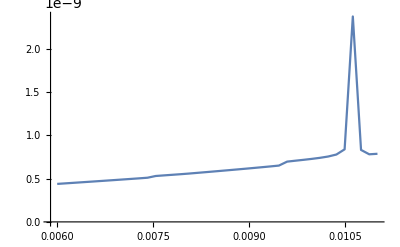

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

```mathematica
2 eV
```

0.008

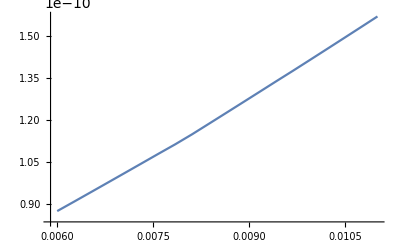

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

```mathematica
eV
```

0.064

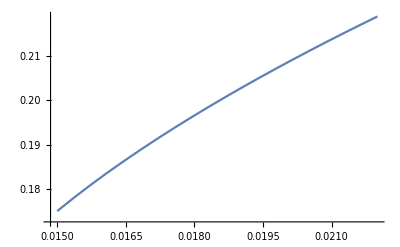

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

```mathematica
2 eV
```

0.032

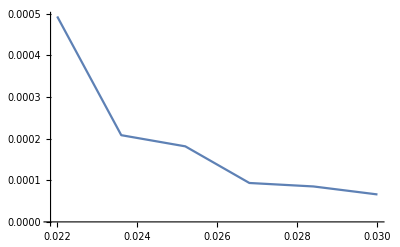

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

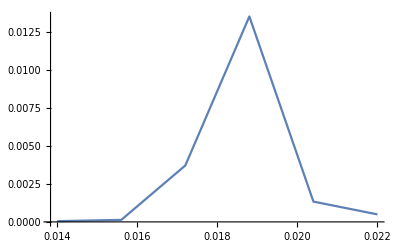

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

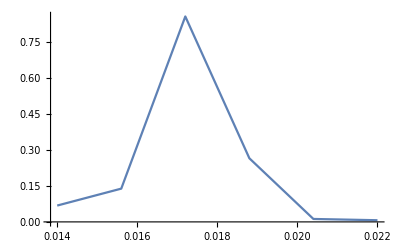

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

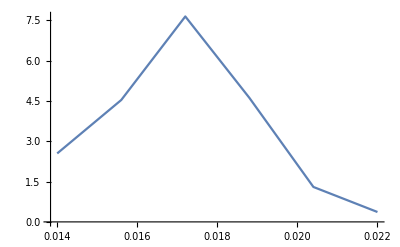

```mathematica
ListLinePlot[Re[NoiseList],PlotRange->All]
```

```mathematica
0.2 0.08
```

0.016

```mathematica
NoiseList
```

{{0.022,0.0000543882+3.45211×10^-10 ⅈ},{0.0236,0.0000510861+2.25598×10^-10 ⅈ},{0.0252,0.000643728+3.84336×10^-9 ⅈ},{0.0268,0.0469057+4.57176×10^-7 ⅈ},{0.0284,0.00544396+5.42468×10^-9 ⅈ},{0.03,0.00116359+1.46273×10^-9 ⅈ}}

```mathematica
NoiseList
```

{{0.022,0},{0.0236,0},{0.0252,0},{0.0268,0},{0.0284,0},{0.03,0.00116359+1.46273×10^-9 ⅈ}}

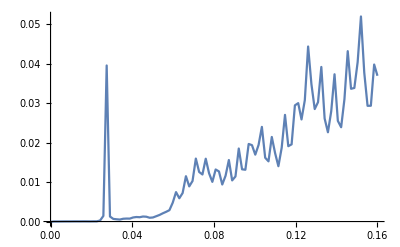

```mathematica
ListLinePlot[Re[NoiseList]]
```

```mathematica
NoiseList//MatrixForm
```

(0. | -0.0000903624+0.000124337 ⅈ
0.00161616 | 0.0000101184+9.55701×10^-8 ⅈ
0.00323232 | 9.30921×10^-6+2.35628×10^-8 ⅈ
0.00484848 | 0.00001578+1.04138×10^-8 ⅈ
0.00646465 | 0.0000276468+5.85625×10^-9 ⅈ
0.00808081 | 0.0000309547+3.68421×10^-9 ⅈ
0.00969697 | 0.0000280405+2.53053×10^-9 ⅈ
0.0113131 | 0.0000413748+1.8338×10^-9 ⅈ
0.0129293 | 0.0000430344+1.38155×10^-9 ⅈ
0.0145455 | 0.0000380746+1.06845×10^-9 ⅈ
0.0161616 | 0.0000489674+8.42361×10^-10 ⅈ
0.0177778 | 0.0000444915+6.70119×10^-10 ⅈ
0.0193939 | 0.0000353909+5.32271×10^-10 ⅈ
0.0210101 | 0.0000487234+4.14051×10^-10 ⅈ
0.0226263 | 0.0000497512+3.00661×10^-10 ⅈ
0.0242424 | 0.000260677+1.87906×10^-9 ⅈ
0.0258586 | 0.00142344+9.20194×10^-9 ⅈ
0.0274747 | 0.0395331+3.88934×10^-8 ⅈ
0.0290909 | 0.00127624+2.6674×10^-9 ⅈ
0.0307071 | 0.000667874+1.05299×10^-9 ⅈ
0.0323232 | 0.000571252+6.28231×10^-10 ⅈ
0.0339394 | 0.000499405+4.44514×10^-10 ⅈ
0.0355556 | 0.00070528+3.42894×10^-10 ⅈ
0.0371717 | 0.000752534+2.77685×10^-10 ⅈ
0.0387879 | 0.000742464+2.31879×10^-10 ⅈ
0.040404 | 0.0010315+1.97676×10^-10 ⅈ
0.0420202 | 0.00114642+1.71038×10^-10 ⅈ
0.0436364 | 0.0010978+1.49822×10^-10 ⅈ
0.0452525 | 0.00126927+1.32434×10^-10 ⅈ
0.0468687 | 0.00122139+1.17976×10^-10 ⅈ
0.0484848 | 0.000961144+1.09309×10^-10 ⅈ
0.050101 | 0.00102956+1.00489×10^-10 ⅈ
0.0517172 | 0.00134592+5.19644×10^-10 ⅈ
0.0533333 | 0.00166888+1.12409×10^-9 ⅈ
0.0549495 | 0.00208792+1.47811×10^-9 ⅈ
0.0565657 | 0.00245896+1.39008×10^-9 ⅈ
0.0581818 | 0.0028811+1.34171×10^-9 ⅈ
0.059798 | 0.00476932+1.25656×10^-9 ⅈ
0.0614141 | 0.00745363+1.14398×10^-9 ⅈ
0.0630303 | 0.00589875+1.01228×10^-9 ⅈ
0.0646465 | 0.00722665+8.67474×10^-10 ⅈ
0.0662626 | 0.011485+7.13319×10^-10 ⅈ
0.0678788 | 0.00890569+5.52763×10^-10 ⅈ
0.0694949 | 0.0102727+3.8632×10^-10 ⅈ
0.0711111 | 0.0159472+2.16779×10^-10 ⅈ
0.0727273 | 0.0125567+4.23772×10^-11 ⅈ
0.0743434 | 0.0119207-1.28537×10^-10 ⅈ
0.0759596 | 0.0159215+4.14024×10^-8 ⅈ
0.0775758 | 0.012242+8.54973×10^-8 ⅈ
0.0791919 | 0.0100493+1.12035×10^-7 ⅈ
0.0808081 | 0.013183+1.31765×10^-7 ⅈ
0.0824242 | 0.0126979+1.48553×10^-7 ⅈ
0.0840404 | 0.00938475+1.62438×10^-7 ⅈ
0.0856566 | 0.011604+1.74475×10^-7 ⅈ
0.0872727 | 0.0155809+1.85077×10^-7 ⅈ
0.0888889 | 0.0104217+1.94524×10^-7 ⅈ
0.0905051 | 0.0114219+2.03015×10^-7 ⅈ
0.0921212 | 0.0184971+2.10701×10^-7 ⅈ
0.0937374 | 0.0132293+2.17703×10^-7 ⅈ
0.0953535 | 0.0131183+2.24084×10^-7 ⅈ
0.0969697 | 0.0196584+2.29938×10^-7 ⅈ
0.0985859 | 0.0193505+2.35299×10^-7 ⅈ
0.100202 | 0.0169439+2.40251×10^-7 ⅈ
0.101818 | 0.0194121+2.44991×10^-7 ⅈ
0.103434 | 0.0239785+2.49371×10^-7 ⅈ
0.105051 | 0.0161668+2.53446×10^-7 ⅈ
0.106667 | 0.0152486+2.57242×10^-7 ⅈ
0.108283 | 0.0214257+2.60781×10^-7 ⅈ
0.109899 | 0.0173372+2.64094×10^-7 ⅈ
0.111515 | 0.0140122+2.67181×10^-7 ⅈ
0.113131 | 0.0187071+2.70072×10^-7 ⅈ
0.114747 | 0.0270206+2.72784×10^-7 ⅈ
0.116364 | 0.0190871+2.75324×10^-7 ⅈ
0.11798 | 0.0195515+2.77701×10^-7 ⅈ
0.119596 | 0.0294348+2.79933×10^-7 ⅈ
0.121212 | 0.0299905+2.82031×10^-7 ⅈ
0.122828 | 0.025864+2.83981×10^-7 ⅈ
0.124444 | 0.0307333+2.85813×10^-7 ⅈ
0.126061 | 0.0443396+2.87527×10^-7 ⅈ
0.127677 | 0.0348238+2.89127×10^-7 ⅈ
0.129293 | 0.0284924+2.90605×10^-7 ⅈ
0.130909 | 0.0302402+2.92014×10^-7 ⅈ
0.132525 | 0.0391624+2.93305×10^-7 ⅈ
0.134141 | 0.0261055+2.94504×10^-7 ⅈ
0.135758 | 0.0226164+2.95608×10^-7 ⅈ
0.137374 | 0.027942+2.9663×10^-7 ⅈ
0.13899 | 0.0373078+2.97558×10^-7 ⅈ
0.140606 | 0.0255118+2.98406×10^-7 ⅈ
0.142222 | 0.0238898+2.99173×10^-7 ⅈ
0.143838 | 0.0309923+2.99856×10^-7 ⅈ
0.145455 | 0.0431632+3.00456×10^-7 ⅈ
0.147071 | 0.0336245+3.00984×10^-7 ⅈ
0.148687 | 0.0338406+3.01428×10^-7 ⅈ
0.150303 | 0.0403891+3.01791×10^-7 ⅈ
0.151919 | 0.0519515+3.02072×10^-7 ⅈ
0.153535 | 0.0377417+3.02274×10^-7 ⅈ
0.155152 | 0.0293132+3.02385×10^-7 ⅈ
0.156768 | 0.0293346+3.02407×10^-7 ⅈ
0.158384 | 0.0397708+3.02322×10^-7 ⅈ
0.16 | 0.0369242+3.02142×10^-7 ⅈ)

```mathematica
NoiseList[[-1]]
```

{0.16,0.0138821-4.74606×10^-10 ⅈ}

```mathematica
NoiseList[[-1]]
```

{0.16,0.0210352+4.59437×10^-9 ⅈ}

```mathematica
NoiseList[[-1]]
```

{0.16,0.0265699-3.28528×10^-8 ⅈ}

```mathematica
NoiseList[[-1]]
```

{0.16,0.0414716-1.28133×10^-7 ⅈ}

```mathematica
NoiseList[[-1]]
```

{0.16,0.0452034+1.54338×10^-7 ⅈ}

```mathematica
NoiseList[[-1]]
```

{0.16,0.0369231+1.51951×10^-8 ⅈ}

```mathematica
ωmin=0.0;
	ωmax=2eV;
	ωsteps=(ωmax-ωmin)/(Nω); (*Energy*)

		Table[(i-1/2)ωsteps+ωmin+I η,{i,1,Nω}]//MatrixForm
```

```mathematica
ωmax
```

0.048

```mathematica
ωsteps
```

0.000048

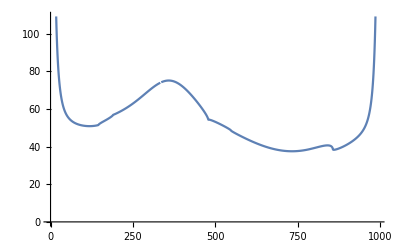

```mathematica
ListLinePlot[Noise]
```

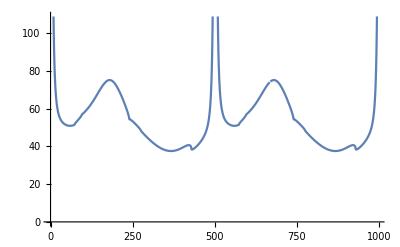

```mathematica
ListLinePlot[Noise]
```

```mathematica
Noise//MatrixForm
```

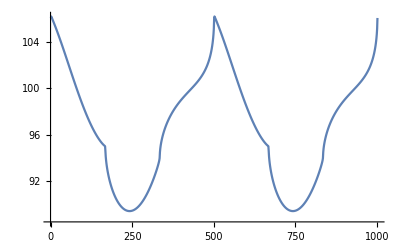

```mathematica
ListLinePlot[Noise]
```

```mathematica
ListLinePlot[Noise]
```

-Graphics-

```mathematica
ListLinePlot[Noise]
```

-Graphics-

```mathematica
Noise
```

{784.521+0.0000612677 ⅈ,673.471+7.03128×10^-9 ⅈ,479.73+5.15454×10^-10 ⅈ,333.18+4.39791×10^-10 ⅈ,241.801+3.29635×10^-10 ⅈ,185.62+1.38254×10^-10 ⅈ,149.88-3.11452×10^-11 ⅈ,126.15+3.21914×10^-11 ⅈ,109.745+1.54186×10^-11 ⅈ,97.9975+8.15024×10^-12 ⅈ,89.3258+3.16039×10^-12 ⅈ,82.7569-1.61397×10^-11 ⅈ,77.6696+3.29203×10^-12 ⅈ,73.6536-5.0541×10^-12 ⅈ,70.4302+5.10367×10^-12 ⅈ,67.8051+3.06587×10^-12 ⅈ,65.6396+9.7291×10^-13 ⅈ,63.8327+1.31605×10^-12 ⅈ,62.3096-3.88271×10^-12 ⅈ,61.0138+6.21416×10^-13 ⅈ,59.9022+1.55649×10^-12 ⅈ,58.9414-1.50943×10^-12 ⅈ,58.1051+2.13563×10^-14 ⅈ,57.3726-8.12949×10^-13 ⅈ,56.7273-6.15164×10^-13 ⅈ,56.1556-7.41913×10^-14 ⅈ,55.6467+1.66194×10^-13 ⅈ,55.1916-2.75366×10^-13 ⅈ,54.7829-1.05132×10^-13 ⅈ,54.4144+2.70692×10^-13 ⅈ,54.0809+2.87096×10^-13 ⅈ,53.7782+2.70131×10^-13 ⅈ,53.5025-3.12602×10^-13 ⅈ,53.2509-1.43171×10^-13 ⅈ,53.0206-1.66278×10^-14 ⅈ,52.8094-1.50334×10^-13 ⅈ,52.6154+7.74481×10^-14 ⅈ,52.437+6.31893×10^-15 ⅈ,52.2726+7.13388×10^-14 ⅈ,52.1212+1.96749×10^-14 ⅈ,51.9815+1.80265×10^-14 ⅈ,51.8528-5.87041×10^-14 ⅈ,51.7343+1.83714×10^-14 ⅈ,51.6251-2.04835×10^-14 ⅈ,51.5249-2.00536×10^-13 ⅈ,51.433-6.85218×10^-14 ⅈ,51.3489+4.80779×10^-14 ⅈ,51.2725-5.77309×10^-14 ⅈ,51.2032+2.51452×10^-14 ⅈ,51.1409-6.17165×10^-14 ⅈ,51.0853+7.74645×10^-14 ⅈ,51.0362-3.37273×10^-14 ⅈ,50.9934-8.28299×10^-14 ⅈ,50.9569-2.88614×10^-14 ⅈ,50.9265+3.09846×10^-14 ⅈ,50.9021+1.40207×10^-14 ⅈ,50.8837+2.82499×10^-14 ⅈ,50.8712-2.91395×10^-14 ⅈ,50.8647+3.18189×10^-14 ⅈ,50.8641+1.61229×10^-14 ⅈ,50.8694+4.13129×10^-14 ⅈ,50.8807+1.8415×10^-14 ⅈ,50.898-1.80174×10^-14 ⅈ,50.9214+5.71318×10^-15 ⅈ,50.951+2.89383×10^-14 ⅈ,50.987+8.21631×10^-14 ⅈ,51.0294-8.48979×10^-14 ⅈ,51.0784+4.64451×10^-15 ⅈ,51.1344-3.30277×10^-14 ⅈ,51.1978-3.7669×10^-14 ⅈ,51.2692+2.23181×10^-14 ⅈ,51.3506+6.53801×10^-14 ⅈ,51.4592-3.57277×10^-14 ⅈ,51.8574-3.20423×10^-14 ⅈ,52.1381-5.79866×10^-14 ⅈ,52.3768-4.79856×10^-14 ⅈ,52.5965+7.10539×10^-14 ⅈ,52.8052-4.208×10^-15 ⅈ,53.0074-1.22087×10^-13 ⅈ,53.2056-6.1588×10^-14 ⅈ,53.4017-3.37106×10^-15 ⅈ,53.5969+1.21739×10^-13 ⅈ,53.7923+5.77031×10^-14 ⅈ,53.9889+3.4221×10^-15 ⅈ,54.1876+3.10796×10^-14 ⅈ,54.3892-3.28759×10^-14 ⅈ,54.5945-2.41981×10^-14 ⅈ,54.8045+4.16812×10^-14 ⅈ,55.0203+2.97637×10^-13 ⅈ,55.2431-7.89753×10^-14 ⅈ,55.4748+9.99939×10^-14 ⅈ,55.7181+3.06424×10^-13 ⅈ,55.9777+1.14252×10^-14 ⅈ,56.2634+1.54102×10^-13 ⅈ,56.6078+1.84508×10^-13 ⅈ,56.9283-1.06093×10^-13 ⅈ,57.0719+3.07304×10^-14 ⅈ,57.2244-6.53192×10^-14 ⅈ,57.3829+1.032×10^-13 ⅈ,57.5459-1.5146×10^-13 ⅈ,57.7126-1.14373×10^-13 ⅈ,57.8829+2.07074×10^-13 ⅈ,58.0565-3.68619×10^-13 ⅈ,58.2333-3.64266×10^-14 ⅈ,58.4134+2.5849×10^-13 ⅈ,58.5968+1.37406×10^-13 ⅈ,58.7835-3.88139×10^-14 ⅈ,58.9735-3.36218×10^-13 ⅈ,59.1669-8.8051×10^-14 ⅈ,59.3637+2.7768×10^-13 ⅈ,59.564-2.82553×10^-13 ⅈ,59.7679+1.64673×10^-13 ⅈ,59.9753+2.83841×10^-13 ⅈ,60.1863+1.31178×10^-12 ⅈ,60.401+4.0653×10^-14 ⅈ,60.6193+2.30398×10^-13 ⅈ,60.8413-3.1203×10^-14 ⅈ,61.0671+2.59985×10^-13 ⅈ,61.2965+6.98273×10^-13 ⅈ,61.5297+4.34236×10^-13 ⅈ,61.7666-8.66927×10^-13 ⅈ,62.0071+1.08739×10^-13 ⅈ,62.2513+6.40313×10^-13 ⅈ,62.4992+4.24493×10^-13 ⅈ,62.7506-7.44815×10^-13 ⅈ,63.0055-1.12514×10^-12 ⅈ,63.2639-2.08456×10^-13 ⅈ,63.5256-1.88932×10^-12 ⅈ,63.7907+7.67127×10^-13 ⅈ,64.0589+2.69948×10^-12 ⅈ,64.3301+1.83975×10^-12 ⅈ,64.6043+4.03333×10^-13 ⅈ,64.8813-1.08248×10^-12 ⅈ,65.1609+2.28095×10^-12 ⅈ,65.443+1.68736×10^-12 ⅈ,65.7273+2.82305×10^-12 ⅈ,66.0137+1.50533×10^-12 ⅈ,66.302-2.3017×10^-14 ⅈ,66.5919-1.59974×10^-12 ⅈ,66.8831+4.86814×10^-12 ⅈ,67.1754-1.3978×10^-13 ⅈ,67.4686+3.66754×10^-13 ⅈ,67.7622-6.50854×10^-12 ⅈ,68.0561+4.89442×10^-13 ⅈ,68.3498-1.41408×10^-12 ⅈ,68.643+2.99441×10^-12 ⅈ,68.9354+4.23827×10^-12 ⅈ,69.2265+8.67064×10^-12 ⅈ,69.516-3.31481×10^-12 ⅈ,69.8034-2.611×10^-12 ⅈ,70.0883-1.07939×10^-11 ⅈ,70.3703-1.56335×10^-11 ⅈ,70.6489-4.02229×10^-13 ⅈ,70.9236-1.14738×10^-11 ⅈ,71.1939+1.03489×10^-11 ⅈ,71.4594+1.47107×10^-11 ⅈ,71.7196+9.03777×10^-12 ⅈ,71.9738-2.11102×10^-11 ⅈ,72.2216+1.06895×10^-11 ⅈ,72.4626-2.97658×10^-11 ⅈ,72.6961-2.80939×10^-11 ⅈ,72.9216+1.87773×10^-11 ⅈ,73.1386+5.65851×10^-11 ⅈ,73.3466-2.95318×10^-10 ⅈ,73.545-3.48408×10^-10 ⅈ,73.7334-3.46225×10^-10 ⅈ,73.9113+1.49905×10^-9 ⅈ,74.1011+6.25244×10^-9 ⅈ,74.2565+6.88894×10^-11 ⅈ,74.4+2.98966×10^-10 ⅈ,74.5311+1.94654×10^-11 ⅈ,74.6494+1.19325×10^-10 ⅈ,74.7545-4.54382×10^-11 ⅈ,74.8461-2.02697×10^-12 ⅈ,74.9239+1.6052×10^-11 ⅈ,74.9876-3.57145×10^-12 ⅈ,75.0368+1.51723×10^-11 ⅈ,75.0715+8.22724×10^-12 ⅈ,75.0913-1.36645×10^-12 ⅈ,75.0962-7.2499×10^-13 ⅈ,75.086-2.21764×10^-12 ⅈ,75.0607+8.18493×10^-14 ⅈ,75.0203+3.43645×10^-12 ⅈ,74.9646-1.3791×10^-12 ⅈ,74.8938+1.70175×10^-12 ⅈ,74.8079+7.2758×10^-13 ⅈ,74.7071-9.31575×10^-13 ⅈ,74.5915-1.49658×10^-12 ⅈ,74.4613-4.88548×10^-13 ⅈ,74.3166-1.55387×10^-12 ⅈ,74.1578+6.31089×10^-13 ⅈ,73.9851+3.44785×10^-13 ⅈ,73.7987+1.94718×10^-13 ⅈ,73.5991+2.51974×10^-13 ⅈ,73.3865-1.71507×10^-14 ⅈ,73.1612-1.26156×10^-12 ⅈ,72.9237+1.95153×10^-13 ⅈ,72.6744-1.04396×10^-12 ⅈ,72.4135-1.55987×10^-12 ⅈ,72.1415-2.78961×10^-12 ⅈ,71.8589-6.98138×10^-13 ⅈ,71.5659-8.47429×10^-13 ⅈ,71.263-9.55745×10^-13 ⅈ,70.9506+9.19452×10^-13 ⅈ,70.6291-5.45273×10^-13 ⅈ,70.2988-1.16831×10^-13 ⅈ,69.9601-4.25108×10^-13 ⅈ,69.6134+1.06657×10^-13 ⅈ,69.2589+4.03337×10^-14 ⅈ,68.8971+1.19708×10^-12 ⅈ,68.5283-3.12316×10^-13 ⅈ,68.1526+4.58952×10^-13 ⅈ,67.7705+1.90098×10^-13 ⅈ,67.3821-6.49459×10^-13 ⅈ,66.9876+8.62767×10^-14 ⅈ,66.5874-5.48523×10^-14 ⅈ,66.1814-4.41804×10^-13 ⅈ,65.77+4.20467×10^-13 ⅈ,65.3532-2.09072×10^-13 ⅈ,64.9311-2.18839×10^-13 ⅈ,64.5038-1.75918×10^-13 ⅈ,64.0712-1.98209×10^-13 ⅈ,63.6334-2.68848×10^-14 ⅈ,63.1903-4.35161×10^-13 ⅈ,62.7417+1.68847×10^-13 ⅈ,62.2875-3.52846×10^-13 ⅈ,61.8273+4.52144×10^-13 ⅈ,61.3608-7.24232×10^-14 ⅈ,60.8875-7.25785×10^-14 ⅈ,60.4066+9.56154×10^-14 ⅈ,59.9173-3.3812×10^-14 ⅈ,59.4183+1.96008×10^-13 ⅈ,58.9078-1.90875×10^-13 ⅈ,58.3835+5.31765×10^-14 ⅈ,57.8415-2.1404×10^-13 ⅈ,57.2763-4.20688×10^-14 ⅈ,56.6777+2.88102×10^-13 ⅈ,56.0258+3.03664×10^-14 ⅈ,55.2669+7.08716×10^-14 ⅈ,54.2821-1.6291×10^-13 ⅈ,54.2983+1.60919×10^-13 ⅈ,54.2454-5.74033×10^-14 ⅈ,54.1568+1.33766×10^-13 ⅈ,54.0482+1.28221×10^-13 ⅈ,53.9267-1.51795×10^-14 ⅈ,53.7959-1.14796×10^-13 ⅈ,53.658-1.03105×10^-13 ⅈ,53.5145+9.64093×10^-15 ⅈ,53.3664-1.07866×10^-13 ⅈ,53.2143-1.13251×10^-13 ⅈ,53.0587+1.38763×10^-15 ⅈ,52.9001+5.99454×10^-14 ⅈ,52.7387-1.65936×10^-14 ⅈ,52.5747-2.61098×10^-14 ⅈ,52.4083+1.83281×10^-14 ⅈ,52.2396-7.44165×10^-14 ⅈ,52.0687+2.09135×10^-14 ⅈ,51.8958-3.06451×10^-15 ⅈ,51.7208-6.22801×10^-14 ⅈ,51.5437-1.28836×10^-14 ⅈ,51.3646+3.1106×10^-15 ⅈ,51.1834+4.90926×10^-14 ⅈ,51.0001+3.72686×10^-14 ⅈ,50.8146-1.10868×10^-14 ⅈ,50.6268-2.22494×10^-14 ⅈ,50.4364-3.80173×10^-14 ⅈ,50.2431-5.77413×10^-14 ⅈ,50.0467+7.65075×10^-15 ⅈ,49.8463+1.90387×10^-14 ⅈ,49.6412+9.45371×10^-15 ⅈ,49.4297-5.06531×10^-15 ⅈ,49.2085+8.33815×10^-15 ⅈ,48.97-4.04215×10^-15 ⅈ,48.6752+2.0671×10^-14 ⅈ,48.3022+2.66905×10^-14 ⅈ,48.065-7.07559×10^-15 ⅈ,47.8497-7.65071×10^-15 ⅈ,47.6446-1.02778×10^-14 ⅈ,47.4456+1.83996×10^-14 ⅈ,47.2508+3.03099×10^-14 ⅈ,47.0593-3.94256×10^-14 ⅈ,46.8704+2.48622×10^-15 ⅈ,46.6836+1.12816×10^-14 ⅈ,46.4987+7.6545×10^-15 ⅈ,46.3155-2.33359×10^-14 ⅈ,46.1338-2.4787×10^-15 ⅈ,45.9535-2.94324×10^-15 ⅈ,45.7745-1.99263×10^-15 ⅈ,45.5968+3.10384×10^-14 ⅈ,45.4204+8.02252×10^-15 ⅈ,45.2452+4.66384×10^-15 ⅈ,45.0712-6.68435×10^-15 ⅈ,44.8984+1.46721×10^-15 ⅈ,44.7269-9.01489×10^-15 ⅈ,44.5565+1.77606×10^-15 ⅈ,44.3874-1.64148×10^-14 ⅈ,44.2196+2.14647×10^-14 ⅈ,44.053-1.62125×10^-14 ⅈ,43.8877+6.22086×10^-16 ⅈ,43.7238-6.58586×10^-15 ⅈ,43.5612-9.67622×10^-16 ⅈ,43.4-1.02405×10^-14 ⅈ,43.2402-1.94099×10^-14 ⅈ,43.0819+1.28193×10^-14 ⅈ,42.9251+1.18369×10^-14 ⅈ,42.7697+1.84731×10^-15 ⅈ,42.6159+2.75428×10^-14 ⅈ,42.4638+6.6542×10^-15 ⅈ,42.3132+9.26452×10^-16 ⅈ,42.1643+1.56885×10^-14 ⅈ,42.0171-2.61159×10^-14 ⅈ,41.8716-6.02254×10^-15 ⅈ,41.7279-1.81723×10^-14 ⅈ,41.586-6.01237×10^-15 ⅈ,41.4459+1.22884×10^-14 ⅈ,41.3077+8.91592×10^-15 ⅈ,41.1715-3.00344×10^-14 ⅈ,41.0371-8.03162×10^-15 ⅈ,40.9048+4.83014×10^-16 ⅈ,40.7745-5.62305×10^-15 ⅈ,40.6463+5.84441×10^-15 ⅈ,40.5202+5.5554×10^-15 ⅈ,40.3962+2.2108×10^-16 ⅈ,40.2743+7.19665×10^-15 ⅈ,40.1547-9.41796×10^-15 ⅈ,40.0373+1.05923×10^-14 ⅈ,39.9222-1.73779×10^-15 ⅈ,39.8094+1.13333×10^-14 ⅈ,39.6989-1.27494×10^-14 ⅈ,39.5908+3.23043×10^-17 ⅈ,39.4851-1.81576×10^-14 ⅈ,39.3819+5.50886×10^-15 ⅈ,39.2811+8.98496×10^-15 ⅈ,39.1828+1.71708×10^-14 ⅈ,39.0871+3.00197×10^-15 ⅈ,38.9939-2.27267×10^-15 ⅈ,38.9033-3.7926×10^-15 ⅈ,38.8153+1.33928×10^-14 ⅈ,38.73+1.43634×10^-14 ⅈ,38.6474-1.81451×10^-14 ⅈ,38.5675-1.25149×10^-14 ⅈ,38.4904+5.73959×10^-15 ⅈ,38.416+2.05339×10^-14 ⅈ,38.3444-1.09109×10^-14 ⅈ,38.2756-6.31663×10^-15 ⅈ,38.2097+1.88275×10^-15 ⅈ,38.1467-1.45882×10^-14 ⅈ,38.0865+7.70956×10^-15 ⅈ,38.0293+1.17933×10^-16 ⅈ,37.9751-1.10762×10^-14 ⅈ,37.9238+9.28368×10^-16 ⅈ,37.8755-1.51516×10^-14 ⅈ,37.8302-7.16347×10^-15 ⅈ,37.7879-1.85471×10^-14 ⅈ,37.7487-4.6554×10^-15 ⅈ,37.7126-7.07371×10^-15 ⅈ,37.6796-9.39827×10^-16 ⅈ,37.6497+3.24686×10^-15 ⅈ,37.623-1.54892×10^-14 ⅈ,37.5993-1.15401×10^-14 ⅈ,37.5789+5.89453×10^-15 ⅈ,37.5616-1.92459×10^-14 ⅈ,37.5475+2.153×10^-15 ⅈ,37.5365-5.25227×10^-15 ⅈ,37.5288-8.87455×10^-15 ⅈ,37.5243-7.5429×10^-15 ⅈ,37.5231-2.63548×10^-15 ⅈ,37.525-9.55124×10^-15 ⅈ,37.5302+7.63317×10^-15 ⅈ,37.5386-1.28563×10^-14 ⅈ,37.5502+1.9741×10^-15 ⅈ,37.5651-7.56993×10^-15 ⅈ,37.5831-1.44595×10^-15 ⅈ,37.6044+1.29581×10^-14 ⅈ,37.6289+5.66299×10^-15 ⅈ,37.6566-5.87516×10^-16 ⅈ,37.6874-4.36592×10^-15 ⅈ,37.7214+1.18199×10^-14 ⅈ,37.7586-1.10951×10^-15 ⅈ,37.7988+4.14119×10^-15 ⅈ,37.8422-6.98436×10^-15 ⅈ,37.8886-7.65491×10^-16 ⅈ,37.938-6.77366×10^-15 ⅈ,37.9903-1.85436×10^-15 ⅈ,38.0457+4.34178×10^-15 ⅈ,38.1039-4.85934×10^-16 ⅈ,38.1649+3.75×10^-15 ⅈ,38.2288+1.86396×10^-14 ⅈ,38.2953-8.33486×10^-15 ⅈ,38.3646+2.48525×10^-14 ⅈ,38.4365-4.17435×10^-15 ⅈ,38.5111+8.29886×10^-15 ⅈ,38.5885-3.11596×10^-15 ⅈ,38.6694-2.72506×10^-14 ⅈ,38.7556-1.13702×10^-14 ⅈ,38.8387-3.75944×10^-15 ⅈ,38.9227-8.92943×10^-15 ⅈ,39.008-8.28005×10^-15 ⅈ,39.0945+1.30771×10^-14 ⅈ,39.1821+1.0961×10^-16 ⅈ,39.2706+1.01521×10^-14 ⅈ,39.3598-5.28536×10^-15 ⅈ,39.4496+3.54954×10^-15 ⅈ,39.5396+6.45155×10^-15 ⅈ,39.6295+1.44675×10^-14 ⅈ,39.7192-1.02334×10^-14 ⅈ,39.8081-1.60962×10^-15 ⅈ,39.8959+1.76976×10^-14 ⅈ,39.9823-2.38069×10^-14 ⅈ,40.0667+5.34938×10^-17 ⅈ,40.1486+7.84082×10^-15 ⅈ,40.2274-1.65517×10^-14 ⅈ,40.3024-1.50349×10^-14 ⅈ,40.373+1.17122×10^-14 ⅈ,40.4381-1.09134×10^-14 ⅈ,40.4968-3.41728×10^-15 ⅈ,40.5479-8.94995×10^-15 ⅈ,40.5899+7.09093×10^-15 ⅈ,40.6213+2.08468×10^-14 ⅈ,40.6397+1.08345×10^-14 ⅈ,40.6427+9.8297×10^-15 ⅈ,40.6266+2.11975×10^-14 ⅈ,40.587+2.09467×10^-15 ⅈ,40.517+6.53614×10^-15 ⅈ,40.4067+1.94018×10^-14 ⅈ,40.239-1.03402×10^-14 ⅈ,39.9803+3.14282×10^-14 ⅈ,39.537+5.16832×10^-15 ⅈ,38.4462+1.81416×10^-14 ⅈ,38.2976+1.66136×10^-14 ⅈ,38.3119+9.25094×10^-15 ⅈ,38.3672+2.71876×10^-14 ⅈ,38.4449+1.00285×10^-14 ⅈ,38.5377-7.38521×10^-15 ⅈ,38.6422-1.63983×10^-14 ⅈ,38.7562-9.47435×10^-15 ⅈ,38.8784-2.31068×10^-14 ⅈ,39.0078+9.29573×10^-15 ⅈ,39.144+4.74024×10^-15 ⅈ,39.2862-3.13518×10^-14 ⅈ,39.4343-4.13131×10^-16 ⅈ,39.5878-6.19717×10^-15 ⅈ,39.7467+3.72833×10^-14 ⅈ,39.9108-2.14079×10^-14 ⅈ,40.08-5.01569×10^-15 ⅈ,40.2542-3.06477×10^-14 ⅈ,40.4334-6.46992×10^-15 ⅈ,40.6176-1.43419×10^-14 ⅈ,40.8068-1.53096×10^-15 ⅈ,41.0012+8.63368×10^-16 ⅈ,41.2007-2.45929×10^-14 ⅈ,41.4055+5.52389×10^-15 ⅈ,41.6158+7.36506×10^-16 ⅈ,41.8317-2.69491×10^-14 ⅈ,42.0536+3.29668×10^-14 ⅈ,42.2816+4.64878×10^-14 ⅈ,42.5161-3.64644×10^-14 ⅈ,42.7574+5.05523×10^-14 ⅈ,43.0061+4.08489×10^-16 ⅈ,43.2627+3.91389×10^-14 ⅈ,43.5276-1.64453×10^-14 ⅈ,43.8017+2.75681×10^-14 ⅈ,44.0858-1.00733×10^-13 ⅈ,44.3807-6.04978×10^-14 ⅈ,44.6875-8.6974×10^-15 ⅈ,45.0076+2.06035×10^-14 ⅈ,45.3424+7.56909×10^-14 ⅈ,45.6936-6.34765×10^-14 ⅈ,46.0633+2.15489×10^-15 ⅈ,46.4537+3.27154×10^-14 ⅈ,46.8678-2.93781×10^-14 ⅈ,47.3087+3.64201×10^-14 ⅈ,47.7805+7.38949×10^-14 ⅈ,48.2878-5.6318×10^-14 ⅈ,48.8363+1.498×10^-13 ⅈ,49.4328-3.98952×10^-13 ⅈ,50.0856+1.63734×10^-13 ⅈ,50.8047+2.80279×10^-13 ⅈ,51.6028-3.11363×10^-13 ⅈ,52.4952-2.56357×10^-14 ⅈ,53.5016+2.99218×10^-13 ⅈ,54.6464-1.70233×10^-12 ⅈ,55.9614-1.98396×10^-12 ⅈ,57.4874+1.45611×10^-12 ⅈ,59.2781+2.21048×10^-12 ⅈ,61.4052-2.56082×10^-12 ⅈ,63.9654-4.72873×10^-14 ⅈ,67.0926-6.15006×10^-13 ⅈ,70.9749+2.13387×10^-13 ⅈ,75.8832-8.51897×10^-12 ⅈ,82.2183+1.23212×10^-11 ⅈ,90.5903-1.81026×10^-11 ⅈ,101.959-4.5737×10^-12 ⅈ,117.891+8.86613×10^-11 ⅈ,141.049-4.26807×10^-11 ⅈ,176.139+1.55294×10^-11 ⅈ,231.699+9.1933×10^-12 ⅈ,322.87+2.03226×10^-9 ⅈ,470.781+6.09108×10^-9 ⅈ,669.963+3.31406×10^-8 ⅈ,784.521-0.0000713302 ⅈ,673.471+8.13388×10^-9 ⅈ,479.73-1.25863×10^-9 ⅈ,333.18-1.63399×10^-9 ⅈ,241.801+3.10837×10^-10 ⅈ,185.62+5.0866×10^-12 ⅈ,149.88+1.44211×10^-10 ⅈ,126.15-5.28512×10^-11 ⅈ,109.745-3.63631×10^-11 ⅈ,97.9975+1.35027×10^-11 ⅈ,89.3258-8.31121×10^-12 ⅈ,82.7569+7.36431×10^-12 ⅈ,77.6696+2.91803×10^-12 ⅈ,73.6536-4.81707×10^-12 ⅈ,70.4302+1.02683×10^-12 ⅈ,67.8051+4.69481×10^-12 ⅈ,65.6396-3.2047×10^-12 ⅈ,63.8327-1.95675×10^-12 ⅈ,62.3096+1.26785×10^-12 ⅈ,61.0138+1.90654×10^-12 ⅈ,59.9022-5.14479×10^-13 ⅈ,58.9414+7.6011×10^-13 ⅈ,58.1051+2.33772×10^-13 ⅈ,57.3726+1.76959×10^-13 ⅈ,56.7273+3.3689×10^-13 ⅈ,56.1556+1.08432×10^-13 ⅈ,55.6467-4.16233×10^-13 ⅈ,55.1916+4.2878×10^-13 ⅈ,54.7829-1.66799×10^-13 ⅈ,54.4144+5.26105×10^-13 ⅈ,54.0809-2.44437×10^-13 ⅈ,53.7782+3.20864×10^-13 ⅈ,53.5025+4.23003×10^-14 ⅈ,53.2509+6.47212×10^-14 ⅈ,53.0206-5.49862×10^-14 ⅈ,52.8094-2.71789×10^-13 ⅈ,52.6154-5.37434×10^-14 ⅈ,52.437+1.70372×10^-13 ⅈ,52.2726+6.63664×10^-14 ⅈ,52.1212+1.9325×10^-14 ⅈ,51.9815-1.32127×10^-13 ⅈ,51.8528-9.87929×10^-14 ⅈ,51.7343+6.45051×10^-14 ⅈ,51.6251-5.0437×10^-14 ⅈ,51.5249-1.20293×10^-13 ⅈ,51.433-2.43317×10^-14 ⅈ,51.3489-6.14824×10^-14 ⅈ,51.2725+3.58614×10^-14 ⅈ,51.2032+6.50685×10^-15 ⅈ,51.1409-7.09391×10^-14 ⅈ,51.0853+2.46618×10^-14 ⅈ,51.0362+7.67477×10^-14 ⅈ,50.9934+4.17574×10^-16 ⅈ,50.9569-7.77525×10^-15 ⅈ,50.9265+2.86758×10^-14 ⅈ,50.9021+1.16301×10^-14 ⅈ,50.8837+1.62023×10^-14 ⅈ,50.8712-1.08379×10^-14 ⅈ,50.8647+3.07123×10^-14 ⅈ,50.8641-2.16773×10^-14 ⅈ,50.8694-1.76575×10^-14 ⅈ,50.8807-1.54346×10^-14 ⅈ,50.898-3.75702×10^-14 ⅈ,50.9214-2.68163×10^-14 ⅈ,50.951+2.57533×10^-14 ⅈ,50.987+6.79713×10^-14 ⅈ,51.0294+9.67012×10^-15 ⅈ,51.0784-1.05726×10^-14 ⅈ,51.1344+1.32908×10^-14 ⅈ,51.1978-3.67017×10^-14 ⅈ,51.2692-1.24029×10^-14 ⅈ,51.3506-6.62196×10^-14 ⅈ,51.4592-4.96276×10^-14 ⅈ,51.8574+1.07849×10^-13 ⅈ,52.1381-1.39905×10^-15 ⅈ,52.3768+5.32085×10^-14 ⅈ,52.5965-8.54153×10^-14 ⅈ,52.8052-7.24666×10^-14 ⅈ,53.0074+1.02336×10^-13 ⅈ,53.2056+2.27534×10^-13 ⅈ,53.4017-2.76116×10^-14 ⅈ,53.5969+2.08048×10^-14 ⅈ,53.7923+4.02348×10^-14 ⅈ,53.9889+7.07676×10^-14 ⅈ,54.1876-1.42735×10^-13 ⅈ,54.3892-1.75308×10^-13 ⅈ,54.5945-2.69657×10^-13 ⅈ,54.8045+3.7193×10^-13 ⅈ,55.0203-8.49386×10^-14 ⅈ,55.2431-8.97282×10^-14 ⅈ,55.4748-4.30144×10^-13 ⅈ,55.7181+1.31543×10^-13 ⅈ,55.9777-6.15041×10^-14 ⅈ,56.2634-1.24428×10^-13 ⅈ,56.6078-9.86863×10^-14 ⅈ,56.9283-7.44058×10^-13 ⅈ,57.0719-2.88462×10^-13 ⅈ,57.2244+1.00782×10^-13 ⅈ,57.3829-4.477×10^-13 ⅈ,57.5459-3.40916×10^-13 ⅈ,57.7126-9.53087×10^-14 ⅈ,57.8829+8.42788×10^-13 ⅈ,58.0565-7.02798×10^-13 ⅈ,58.2333-3.70275×10^-13 ⅈ,58.4134-4.68×10^-13 ⅈ,58.5968+4.45775×10^-13 ⅈ,58.7835-1.05166×10^-12 ⅈ,58.9735+1.72488×10^-13 ⅈ,59.1669-7.80868×10^-13 ⅈ,59.3637+1.80867×10^-13 ⅈ,59.564+5.12163×10^-14 ⅈ,59.7679+4.51466×10^-13 ⅈ,59.9753-2.0859×10^-13 ⅈ,60.1863+1.24349×10^-13 ⅈ,60.401-4.78887×10^-13 ⅈ,60.6193-4.4503×10^-13 ⅈ,60.8413+6.10249×10^-13 ⅈ,61.0671+8.06775×10^-13 ⅈ,61.2965+4.262×10^-13 ⅈ,61.5297+7.70286×10^-13 ⅈ,61.7666-2.64121×10^-12 ⅈ,62.0071-7.48789×10^-14 ⅈ,62.2513-1.30141×10^-12 ⅈ,62.4992+1.12071×10^-12 ⅈ,62.7506+1.40733×10^-13 ⅈ,63.0055+8.43845×10^-13 ⅈ,63.2639-6.89702×10^-13 ⅈ,63.5256+2.20389×10^-14 ⅈ,63.7907-2.95784×10^-13 ⅈ,64.0589-4.62705×10^-12 ⅈ,64.3301-4.73171×10^-13 ⅈ,64.6043-1.1521×10^-12 ⅈ,64.8813+1.43358×10^-12 ⅈ,65.1609+1.44608×10^-13 ⅈ,65.443-2.23036×10^-13 ⅈ,65.7273+2.77897×10^-12 ⅈ,66.0137+2.06158×10^-12 ⅈ,66.302+9.91276×10^-13 ⅈ,66.5919+6.892×10^-13 ⅈ,66.8831+5.77855×10^-12 ⅈ,67.1754+9.11035×10^-13 ⅈ,67.4686-4.27387×10^-12 ⅈ,67.7622+8.70391×10^-13 ⅈ,68.0561-9.81858×10^-13 ⅈ,68.3498+9.24631×10^-12 ⅈ,68.643+5.46784×10^-12 ⅈ,68.9354-4.40788×10^-12 ⅈ,69.2265-3.51627×10^-12 ⅈ,69.516+1.94973×10^-12 ⅈ,69.8034+3.26733×10^-12 ⅈ,70.0883-1.65491×10^-12 ⅈ,70.3703+1.15432×10^-11 ⅈ,70.6489+1.92976×10^-11 ⅈ,70.9236+3.10069×10^-12 ⅈ,71.1939-1.48645×10^-11 ⅈ,71.4594-2.96167×10^-11 ⅈ,71.7196-5.67136×10^-13 ⅈ,71.9738+2.34002×10^-11 ⅈ,72.2216+5.624×10^-11 ⅈ,72.4626+1.51748×10^-11 ⅈ,72.6961-6.55835×10^-11 ⅈ,72.9216+9.93642×10^-11 ⅈ,73.1386-4.32065×10^-11 ⅈ,73.3466-1.12203×10^-10 ⅈ,73.545-2.19208×10^-10 ⅈ,73.7334-4.41704×10^-10 ⅈ,73.9113-3.75743×10^-10 ⅈ,74.1011+2.56646×10^-8 ⅈ,74.2565-8.305×10^-10 ⅈ,74.4+1.49964×10^-11 ⅈ,74.5311+5.83418×10^-11 ⅈ,74.6494+4.79289×10^-11 ⅈ,74.7545+1.60407×10^-11 ⅈ,74.8461+1.87273×10^-11 ⅈ,74.9239+3.2384×10^-11 ⅈ,74.9876+1.40534×10^-12 ⅈ,75.0368-7.33023×10^-13 ⅈ,75.0715-1.32831×10^-11 ⅈ,75.0913+1.70855×10^-11 ⅈ,75.0962-1.43271×10^-11 ⅈ,75.086+5.7892×10^-12 ⅈ,75.0607-6.64599×10^-13 ⅈ,75.0203+5.51717×10^-12 ⅈ,74.9646+5.01049×10^-13 ⅈ,74.8938-1.89345×10^-12 ⅈ,74.8079+1.87095×10^-12 ⅈ,74.7071+2.05262×10^-12 ⅈ,74.5915+7.99679×10^-13 ⅈ,74.4613-1.97452×10^-12 ⅈ,74.3166-9.9705×10^-13 ⅈ,74.1578+2.71973×10^-12 ⅈ,73.9851-1.16649×10^-12 ⅈ,73.7987-2.27666×10^-12 ⅈ,73.5991-7.2756×10^-13 ⅈ,73.3865-1.80764×10^-12 ⅈ,73.1612-5.76757×10^-13 ⅈ,72.9237+7.13651×10^-13 ⅈ,72.6744-1.2572×10^-13 ⅈ,72.4135-9.8896×10^-14 ⅈ,72.1415+6.04637×10^-13 ⅈ,71.8589-1.68447×10^-12 ⅈ,71.5659-2.62588×10^-13 ⅈ,71.263-4.25921×10^-13 ⅈ,70.9506+8.28595×10^-13 ⅈ,70.6291+9.54445×10^-13 ⅈ,70.2988-1.6014×10^-14 ⅈ,69.9601-7.92995×10^-14 ⅈ,69.6134-4.07263×10^-14 ⅈ,69.2589+8.80415×10^-13 ⅈ,68.8971+1.86018×10^-12 ⅈ,68.5283-1.11686×10^-12 ⅈ,68.1526+1.07771×10^-12 ⅈ,67.7705+2.87492×10^-13 ⅈ,67.3821+7.67837×10^-13 ⅈ,66.9876-1.4072×10^-13 ⅈ,66.5874-1.4139×10^-12 ⅈ,66.1814-2.5573×10^-13 ⅈ,65.77+7.08512×10^-13 ⅈ,65.3532+4.45879×10^-13 ⅈ,64.9311+3.12361×10^-13 ⅈ,64.5038-2.04193×10^-13 ⅈ,64.0712+1.00264×10^-12 ⅈ,63.6334+6.15088×10^-13 ⅈ,63.1903+3.23367×10^-13 ⅈ,62.7417+5.48758×10^-15 ⅈ,62.2875-2.54952×10^-14 ⅈ,61.8273-2.35211×10^-13 ⅈ,61.3608-4.17248×10^-13 ⅈ,60.8875-3.32937×10^-13 ⅈ,60.4066+4.40448×10^-13 ⅈ,59.9173+1.98379×10^-13 ⅈ,59.4183-1.21229×10^-13 ⅈ,58.9078-1.30553×10^-13 ⅈ,58.3835+3.10389×10^-13 ⅈ,57.8415+5.49564×10^-14 ⅈ,57.2763-5.64377×10^-14 ⅈ,56.6777-2.58089×10^-13 ⅈ,56.0258-3.20743×10^-13 ⅈ,55.2669+2.50238×10^-13 ⅈ,54.2821+1.37373×10^-13 ⅈ,54.2983-1.86666×10^-13 ⅈ,54.2454-1.40133×10^-14 ⅈ,54.1568-2.42913×10^-13 ⅈ,54.0482+2.20994×10^-13 ⅈ,53.9267+8.0479×10^-14 ⅈ,53.7959-6.5712×10^-14 ⅈ,53.658-2.85562×10^-13 ⅈ,53.5145-1.09541×10^-13 ⅈ,53.3664+2.90125×10^-14 ⅈ,53.2143+1.62599×10^-13 ⅈ,53.0587+1.47885×10^-13 ⅈ,52.9001+1.39003×10^-13 ⅈ,52.7387+7.14112×10^-14 ⅈ,52.5747-1.38927×10^-14 ⅈ,52.4083-3.40201×10^-14 ⅈ,52.2396+7.58462×10^-14 ⅈ,52.0687-9.65562×10^-14 ⅈ,51.8958-4.45638×10^-14 ⅈ,51.7208+1.68792×10^-14 ⅈ,51.5437-3.56213×10^-14 ⅈ,51.3646+1.31183×10^-13 ⅈ,51.1834-4.07013×10^-14 ⅈ,51.0001-6.14672×10^-14 ⅈ,50.8146+7.98412×10^-14 ⅈ,50.6268-8.92072×10^-15 ⅈ,50.4364-7.75853×10^-14 ⅈ,50.2431+2.31909×10^-14 ⅈ,50.0467+2.27774×10^-14 ⅈ,49.8463+3.66317×10^-14 ⅈ,49.6412+2.63207×10^-14 ⅈ,49.4297-9.35254×10^-14 ⅈ,49.2085+2.01027×10^-14 ⅈ,48.97-3.11607×10^-14 ⅈ,48.6752+4.69662×10^-14 ⅈ,48.3022+1.38787×10^-14 ⅈ,48.065-2.08981×10^-14 ⅈ,47.8497-5.4262×10^-15 ⅈ,47.6446-1.65242×10^-14 ⅈ,47.4456-2.54538×10^-14 ⅈ,47.2508-3.41528×10^-14 ⅈ,47.0593-2.66815×10^-14 ⅈ,46.8704-8.18937×10^-15 ⅈ,46.6836+2.62798×10^-14 ⅈ,46.4987-7.55251×10^-16 ⅈ,46.3155-2.12658×10^-14 ⅈ,46.1338+8.38007×10^-16 ⅈ,45.9535-6.64815×10^-14 ⅈ,45.7745-1.50588×10^-14 ⅈ,45.5968+2.92817×10^-17 ⅈ,45.4204+3.34366×10^-15 ⅈ,45.2452-2.73561×10^-14 ⅈ,45.0712-1.00764×10^-14 ⅈ,44.8984+9.09552×10^-15 ⅈ,44.7269+1.92789×10^-15 ⅈ,44.5565+7.54193×10^-15 ⅈ,44.3874-1.57939×10^-14 ⅈ,44.2196-9.28634×10^-15 ⅈ,44.053-1.08002×10^-14 ⅈ,43.8877-7.19686×10^-15 ⅈ,43.7238-2.4241×10^-14 ⅈ,43.5612+4.18944×10^-15 ⅈ,43.4+3.8343×10^-15 ⅈ,43.2402+8.79861×10^-15 ⅈ,43.0819-4.67391×10^-15 ⅈ,42.9251-1.13425×10^-14 ⅈ,42.7697-1.03227×10^-14 ⅈ,42.6159+1.59173×10^-16 ⅈ,42.4638-1.81134×10^-14 ⅈ,42.3132-2.67473×10^-16 ⅈ,42.1643+9.71007×10^-15 ⅈ,42.0171+8.66463×10^-15 ⅈ,41.8716+1.93865×10^-14 ⅈ,41.7279-7.98796×10^-15 ⅈ,41.586+1.04362×10^-14 ⅈ,41.4459+6.7359×10^-15 ⅈ,41.3077+1.15087×10^-14 ⅈ,41.1715+1.81381×10^-15 ⅈ,41.0371-3.17514×10^-14 ⅈ,40.9048+1.76138×10^-14 ⅈ,40.7745+7.53352×10^-15 ⅈ,40.6463-1.05498×10^-14 ⅈ,40.5202-1.39872×10^-14 ⅈ,40.3962+3.07487×10^-14 ⅈ,40.2743-6.05865×10^-16 ⅈ,40.1547-6.4776×10^-15 ⅈ,40.0373-3.56439×10^-15 ⅈ,39.9222+4.41379×10^-15 ⅈ,39.8094-6.84512×10^-15 ⅈ,39.6989+1.04346×10^-14 ⅈ,39.5908-1.9594×10^-15 ⅈ,39.4851+2.88935×10^-15 ⅈ,39.3819-6.45868×10^-15 ⅈ,39.2811-1.02827×10^-14 ⅈ,39.1828+6.36153×10^-15 ⅈ,39.0871+1.67373×10^-15 ⅈ,38.9939+1.04947×10^-14 ⅈ,38.9033-4.66696×10^-15 ⅈ,38.8153-1.42788×10^-14 ⅈ,38.73+4.82223×10^-15 ⅈ,38.6474-1.84023×10^-15 ⅈ,38.5675-3.34908×10^-15 ⅈ,38.4904-1.55205×10^-14 ⅈ,38.416-1.20034×10^-14 ⅈ,38.3444+7.82593×10^-15 ⅈ,38.2756-1.06124×10^-14 ⅈ,38.2097-1.13422×10^-15 ⅈ,38.1467+1.48779×10^-14 ⅈ,38.0865-5.03281×10^-15 ⅈ,38.0293-4.8815×10^-15 ⅈ,37.9751-1.24496×10^-14 ⅈ,37.9238-3.07153×10^-15 ⅈ,37.8755-1.31398×10^-14 ⅈ,37.8302-1.2008×10^-14 ⅈ,37.7879+1.41616×10^-14 ⅈ,37.7487+9.40397×10^-16 ⅈ,37.7126+1.78494×10^-14 ⅈ,37.6796-8.48865×10^-15 ⅈ,37.6497-1.43956×10^-14 ⅈ,37.623+1.41549×10^-15 ⅈ,37.5993-4.77099×10^-15 ⅈ,37.5789-1.45967×10^-14 ⅈ,37.5616+1.60271×10^-15 ⅈ,37.5475-2.03199×10^-15 ⅈ,37.5365-1.37403×10^-15 ⅈ,37.5288-1.37026×10^-14 ⅈ,37.5243-2.065×10^-15 ⅈ,37.5231+1.26604×10^-14 ⅈ,37.525+4.08545×10^-15 ⅈ,37.5302+7.74515×10^-15 ⅈ,37.5386+4.22656×10^-15 ⅈ,37.5502-1.15322×10^-14 ⅈ,37.5651+2.15451×10^-15 ⅈ,37.5831+9.13495×10^-15 ⅈ,37.6044-1.27783×10^-14 ⅈ,37.6289+7.84298×10^-15 ⅈ,37.6566+4.27234×10^-15 ⅈ,37.6874-2.028×10^-15 ⅈ,37.7214-4.6468×10^-15 ⅈ,37.7586-3.54512×10^-15 ⅈ,37.7988+1.23597×10^-14 ⅈ,37.8422-1.5245×10^-14 ⅈ,37.8886+3.36301×10^-15 ⅈ,37.938-1.57422×10^-15 ⅈ,37.9903+6.43567×10^-15 ⅈ,38.0457-2.86654×10^-14 ⅈ,38.1039+2.45407×10^-14 ⅈ,38.1649+2.63891×10^-14 ⅈ,38.2288-3.27781×10^-15 ⅈ,38.2953-1.24091×10^-14 ⅈ,38.3646-8.74267×10^-15 ⅈ,38.4365-1.04994×10^-14 ⅈ,38.5111-2.56655×10^-14 ⅈ,38.5885+4.44842×10^-15 ⅈ,38.6694-7.34068×10^-15 ⅈ,38.7556-9.21229×10^-16 ⅈ,38.8387-8.9457×10^-18 ⅈ,38.9227-1.33429×10^-14 ⅈ,39.008-4.44127×10^-15 ⅈ,39.0945+1.69305×10^-14 ⅈ,39.1821+1.37873×10^-15 ⅈ,39.2706-5.07703×10^-16 ⅈ,39.3598-2.24168×10^-14 ⅈ,39.4496+3.67459×10^-15 ⅈ,39.5396-3.74685×10^-15 ⅈ,39.6295-1.76635×10^-14 ⅈ,39.7192+1.52003×10^-14 ⅈ,39.8081-1.8022×10^-15 ⅈ,39.8959+8.79833×10^-15 ⅈ,39.9823+3.20727×10^-15 ⅈ,40.0667-1.64131×10^-14 ⅈ,40.1486-1.651×10^-14 ⅈ,40.2274+1.60237×10^-14 ⅈ,40.3024-1.80194×10^-14 ⅈ,40.373+1.6016×10^-14 ⅈ,40.4381+2.77325×10^-15 ⅈ,40.4968+8.2176×10^-15 ⅈ,40.5479+1.04269×10^-14 ⅈ,40.5899-7.69652×10^-15 ⅈ,40.6213-5.77021×10^-15 ⅈ,40.6397-1.48442×10^-14 ⅈ,40.6427-9.18287×10^-15 ⅈ,40.6266+1.70601×10^-14 ⅈ,40.587+1.02864×10^-14 ⅈ,40.517-2.38779×10^-14 ⅈ,40.4067+2.39357×10^-14 ⅈ,40.239+9.51819×10^-15 ⅈ,39.9803-2.58422×10^-14 ⅈ,39.537+3.55218×10^-14 ⅈ,38.4462+2.38482×10^-14 ⅈ,38.2976+6.56217×10^-15 ⅈ,38.3119+2.04985×10^-15 ⅈ,38.3672-1.75839×10^-14 ⅈ,38.4449-9.55182×10^-15 ⅈ,38.5377+1.75191×10^-14 ⅈ,38.6422-4.63456×10^-14 ⅈ,38.7562+1.20001×10^-14 ⅈ,38.8784-5.25336×10^-15 ⅈ,39.0078+3.19228×10^-14 ⅈ,39.144+1.07792×10^-14 ⅈ,39.2862-9.58491×10^-15 ⅈ,39.4343-1.57388×10^-14 ⅈ,39.5878-7.25317×10^-15 ⅈ,39.7467-7.94702×10^-15 ⅈ,39.9108-3.60995×10^-15 ⅈ,40.08+9.95536×10^-15 ⅈ,40.2542-1.28549×10^-14 ⅈ,40.4334-1.1273×10^-14 ⅈ,40.6176+3.35942×10^-15 ⅈ,40.8068-3.97709×10^-14 ⅈ,41.0012+2.04387×10^-14 ⅈ,41.2007-2.6131×10^-14 ⅈ,41.4055+9.98109×10^-16 ⅈ,41.6158+1.6477×10^-15 ⅈ,41.8317-3.67194×10^-15 ⅈ,42.0536-5.56848×10^-15 ⅈ,42.2816+1.45323×10^-14 ⅈ,42.5161-2.4315×10^-14 ⅈ,42.7574+5.99284×10^-14 ⅈ,43.0061-4.06668×10^-15 ⅈ,43.2627+3.22539×10^-14 ⅈ,43.5276-5.34008×10^-14 ⅈ,43.8017+5.79646×10^-14 ⅈ,44.0858-9.79714×10^-16 ⅈ,44.3807-3.38568×10^-14 ⅈ,44.6875+4.19082×10^-15 ⅈ,45.0076-7.13137×10^-14 ⅈ,45.3424-8.26872×10^-14 ⅈ,45.6936-2.18094×10^-14 ⅈ,46.0633-6.04697×10^-14 ⅈ,46.4537-2.41369×10^-14 ⅈ,46.8678-1.01254×10^-14 ⅈ,47.3087-8.81738×10^-14 ⅈ,47.7805+7.66199×10^-14 ⅈ,48.2878+8.84392×10^-14 ⅈ,48.8363-1.51199×10^-13 ⅈ,49.4328-5.16679×10^-13 ⅈ,50.0856+1.8572×10^-13 ⅈ,50.8047-4.94108×10^-13 ⅈ,51.6028-1.31757×10^-13 ⅈ,52.4952-2.26189×10^-13 ⅈ,53.5016+5.59512×10^-13 ⅈ,54.6464-1.69129×10^-12 ⅈ,55.9614+9.77647×10^-13 ⅈ,57.4874-6.54152×10^-13 ⅈ,59.2781-9.87312×10^-13 ⅈ,61.4052+4.07299×10^-13 ⅈ,63.9654-2.49731×10^-12 ⅈ,67.0926-2.91433×10^-12 ⅈ,70.9749+4.69687×10^-12 ⅈ,75.8832+1.17966×10^-11 ⅈ,82.2183+7.48762×10^-12 ⅈ,90.5903+1.59975×10^-11 ⅈ,101.959+9.67447×10^-13 ⅈ,117.891-6.23692×10^-11 ⅈ,141.049+1.63754×10^-11 ⅈ,176.139+1.17891×10^-10 ⅈ,231.699-1.43562×10^-10 ⅈ,322.87-2.0148×10^-9 ⅈ,470.781+4.98281×10^-9 ⅈ,669.963-2.28725×10^-8 ⅈ,784.521-0.0000174116 ⅈ}

```mathematica
Noise
```

{106.09+8.99315×10^-13 ⅈ,106.221-6.84195×10^-13 ⅈ,106.162-1.59701×10^-14 ⅈ,106.096+8.89541×10^-14 ⅈ,106.029-8.28601×10^-16 ⅈ,105.96+1.37444×10^-13 ⅈ,105.891-1.7058×10^-14 ⅈ,105.822+1.08261×10^-14 ⅈ,105.751+3.13794×10^-14 ⅈ,105.681+3.26347×10^-15 ⅈ,105.609-8.22582×10^-15 ⅈ,105.538-5.32675×10^-15 ⅈ,105.465+1.79304×10^-14 ⅈ,105.392-5.07051×10^-17 ⅈ,105.319-5.96466×10^-15 ⅈ,105.245+1.29133×10^-14 ⅈ,105.171+4.7962×10^-15 ⅈ,105.096-7.58741×10^-16 ⅈ,105.021+1.0453×10^-14 ⅈ,104.945-1.60254×10^-14 ⅈ,104.869-1.20022×10^-14 ⅈ,104.792-1.05176×10^-14 ⅈ,104.714+1.10854×10^-14 ⅈ,104.637+3.46089×10^-14 ⅈ,104.559+3.67262×10^-15 ⅈ,104.48-1.68099×10^-14 ⅈ,104.401-4.5319×10^-16 ⅈ,104.322+5.84517×10^-15 ⅈ,104.242-9.40335×10^-15 ⅈ,104.162-2.12711×10^-15 ⅈ,104.081-2.70719×10^-14 ⅈ,104.001+8.75327×10^-15 ⅈ,103.92+3.83857×10^-15 ⅈ,103.838-1.22625×10^-15 ⅈ,103.756-7.97457×10^-15 ⅈ,103.674+2.50866×10^-15 ⅈ,103.592+1.45167×10^-14 ⅈ,103.509+5.95714×10^-16 ⅈ,103.426-1.63675×10^-15 ⅈ,103.343+4.63806×10^-15 ⅈ,103.26+7.63996×10^-15 ⅈ,103.176-2.48341×10^-14 ⅈ,103.093-7.36435×10^-15 ⅈ,103.009+1.2167×10^-14 ⅈ,102.925-4.89367×10^-15 ⅈ,102.84-8.40376×10^-15 ⅈ,102.756-7.68142×10^-15 ⅈ,102.672-6.07459×10^-15 ⅈ,102.587+6.83492×10^-15 ⅈ,102.502-4.97126×10^-15 ⅈ,102.418+4.73009×10^-15 ⅈ,102.333+8.58417×10^-15 ⅈ,102.248+8.34637×10^-15 ⅈ,102.163+2.25434×10^-14 ⅈ,102.078-3.6735×10^-15 ⅈ,101.993-1.31629×10^-14 ⅈ,101.908+1.48042×10^-14 ⅈ,101.823+5.11833×10^-15 ⅈ,101.738-4.76481×10^-15 ⅈ,101.653+1.49087×10^-14 ⅈ,101.568-1.07313×10^-14 ⅈ,101.484-8.06263×10^-15 ⅈ,101.399-1.17334×10^-14 ⅈ,101.315-3.37241×10^-15 ⅈ,101.23-2.13874×10^-15 ⅈ,101.146-8.33533×10^-15 ⅈ,101.062+7.99146×10^-15 ⅈ,100.978+5.54259×10^-15 ⅈ,100.894+4.74586×10^-15 ⅈ,100.81+1.79346×10^-14 ⅈ,100.726+1.34295×10^-14 ⅈ,100.643-9.98083×10^-15 ⅈ,100.56+2.03034×10^-14 ⅈ,100.477+1.58946×10^-14 ⅈ,100.394+4.16735×10^-15 ⅈ,100.312+2.29224×10^-16 ⅈ,100.23-2.88738×10^-15 ⅈ,100.148-1.48573×10^-14 ⅈ,100.066+1.79721×10^-14 ⅈ,99.985+2.8428×10^-15 ⅈ,99.904+7.17728×10^-15 ⅈ,99.8233-7.00091×10^-15 ⅈ,99.7429+1.90277×10^-15 ⅈ,99.6629-1.80947×10^-14 ⅈ,99.5832+9.79035×10^-15 ⅈ,99.5038-5.27362×10^-16 ⅈ,99.4248+4.06763×10^-15 ⅈ,99.3462-9.55254×10^-16 ⅈ,99.268-1.31358×10^-15 ⅈ,99.1902+3.77142×10^-15 ⅈ,99.1128+2.17811×10^-15 ⅈ,99.0357+3.88766×10^-15 ⅈ,98.9592-4.02899×10^-15 ⅈ,98.883-5.5415×10^-15 ⅈ,98.8073-8.77712×10^-15 ⅈ,98.732-1.70672×10^-14 ⅈ,98.6572+5.44078×10^-15 ⅈ,98.5829+1.08889×10^-14 ⅈ,98.509-1.13777×10^-15 ⅈ,98.4356+7.68796×10^-15 ⅈ,98.3627-1.21969×10^-15 ⅈ,98.2904+2.54495×10^-15 ⅈ,98.2185-4.90589×10^-15 ⅈ,98.1471-2.33889×10^-14 ⅈ,98.0763-3.01516×10^-15 ⅈ,98.006+2.3051×10^-15 ⅈ,97.9362+2.74541×10^-15 ⅈ,97.867-6.12906×10^-15 ⅈ,97.7983-6.98254×10^-15 ⅈ,97.7302+6.46395×10^-15 ⅈ,97.6627+6.58655×10^-15 ⅈ,97.5957-2.09006×10^-15 ⅈ,97.5294+1.34578×10^-14 ⅈ,97.4636-5.26109×10^-15 ⅈ,97.3984+8.06746×10^-16 ⅈ,97.3338-9.73538×10^-15 ⅈ,97.2698+1.00331×10^-14 ⅈ,97.2065-1.30421×10^-14 ⅈ,97.1437+2.86151×10^-16 ⅈ,97.0816+2.13687×10^-14 ⅈ,97.0201-1.82075×10^-15 ⅈ,96.9593-6.32298×10^-15 ⅈ,96.8991-1.35215×10^-14 ⅈ,96.8396-2.01251×10^-15 ⅈ,96.7807-1.67945×10^-14 ⅈ,96.7225-1.44423×10^-14 ⅈ,96.6649+1.41354×10^-15 ⅈ,96.6081-6.7588×10^-15 ⅈ,96.5519+5.25907×10^-15 ⅈ,96.4964+6.25183×10^-15 ⅈ,96.4416-6.59145×10^-15 ⅈ,96.3875-1.92575×10^-17 ⅈ,96.3341+7.64967×10^-15 ⅈ,96.2814-8.82206×10^-15 ⅈ,96.2294-2.00861×10^-14 ⅈ,96.1782-6.63599×10^-16 ⅈ,96.1277-1.45495×10^-14 ⅈ,96.0779+1.90596×10^-15 ⅈ,96.0288+5.72586×10^-15 ⅈ,95.9806+1.62047×10^-14 ⅈ,95.933-3.87353×10^-15 ⅈ,95.8863-6.82221×10^-15 ⅈ,95.8403+8.94952×10^-15 ⅈ,95.795+1.64674×10^-15 ⅈ,95.7506-1.25976×10^-14 ⅈ,95.7069-3.10673×10^-15 ⅈ,95.6641-5.07713×10^-15 ⅈ,95.6221-1.17773×10^-14 ⅈ,95.5809+5.11752×10^-15 ⅈ,95.5405-1.78755×10^-14 ⅈ,95.501-1.24442×10^-14 ⅈ,95.4623-2.3074×10^-14 ⅈ,95.4245+7.67493×10^-16 ⅈ,95.3876+9.18665×10^-16 ⅈ,95.3516+5.89534×10^-15 ⅈ,95.3165-1.06324×10^-15 ⅈ,95.2824+8.2237×10^-15 ⅈ,95.2493-7.1503×10^-15 ⅈ,95.2171+2.10401×10^-14 ⅈ,95.1861+3.37572×10^-15 ⅈ,95.1561-1.51951×10^-14 ⅈ,95.1273+5.73135×10^-15 ⅈ,95.0997+9.83235×10^-15 ⅈ,95.0733+1.63066×10^-16 ⅈ,95.0481-3.03599×10^-14 ⅈ,95.0236-4.37897×10^-14 ⅈ,94.994+1.59794×10^-13 ⅈ,94.5843-4.18015×10^-13 ⅈ,94.1097-1.31208×10^-13 ⅈ,93.7976-2.06272×10^-14 ⅈ,93.5468+1.12894×10^-14 ⅈ,93.3312+1.91797×10^-14 ⅈ,93.1393-5.46911×10^-15 ⅈ,92.9649-5.31067×10^-15 ⅈ,92.8041+1.96611×10^-14 ⅈ,92.6543-3.3036×10^-15 ⅈ,92.5138+1.91715×10^-14 ⅈ,92.3812-7.09437×10^-16 ⅈ,92.2556+1.82057×10^-14 ⅈ,92.136+6.22994×10^-15 ⅈ,92.0218-3.84303×10^-15 ⅈ,91.9126-1.12151×10^-15 ⅈ,91.8079-1.57894×10^-14 ⅈ,91.7073+5.46177×10^-15 ⅈ,91.6106+3.90707×10^-15 ⅈ,91.5174+6.71662×10^-15 ⅈ,91.4276-9.29178×10^-15 ⅈ,91.3409+3.97827×10^-15 ⅈ,91.2572-1.26414×10^-14 ⅈ,91.1764-8.08906×10^-16 ⅈ,91.0982+5.60139×10^-16 ⅈ,91.0225-1.10263×10^-14 ⅈ,90.9493+4.43403×10^-17 ⅈ,90.8785+5.14868×10^-15 ⅈ,90.81-3.83039×10^-15 ⅈ,90.7436-2.29894×10^-14 ⅈ,90.6793-1.98381×10^-14 ⅈ,90.6171+1.02539×10^-14 ⅈ,90.5568-7.42428×10^-15 ⅈ,90.4985+1.34274×10^-14 ⅈ,90.4421+7.60397×10^-15 ⅈ,90.3874-3.78573×10^-15 ⅈ,90.3346+2.53541×10^-15 ⅈ,90.2835+8.32389×10^-15 ⅈ,90.2341+1.03304×10^-14 ⅈ,90.1863-9.33876×10^-15 ⅈ,90.1402-4.5403×10^-15 ⅈ,90.0957+6.65853×10^-15 ⅈ,90.0527-1.90777×10^-16 ⅈ,90.0113+6.66041×10^-15 ⅈ,89.9714-8.82401×10^-15 ⅈ,89.933-1.67278×10^-15 ⅈ,89.8961-1.71079×10^-14 ⅈ,89.8606-1.54409×10^-15 ⅈ,89.8265-5.5666×10^-15 ⅈ,89.7939-2.00594×10^-15 ⅈ,89.7626-1.35223×10^-15 ⅈ,89.7327-1.93732×10^-15 ⅈ,89.7041+6.14377×10^-15 ⅈ,89.6769+8.08289×10^-15 ⅈ,89.651-2.81395×10^-15 ⅈ,89.6264+2.36338×10^-15 ⅈ,89.6031-4.29346×10^-15 ⅈ,89.5811-8.4411×10^-16 ⅈ,89.5604-3.03329×10^-15 ⅈ,89.5409+8.63034×10^-16 ⅈ,89.5227-8.24304×10^-15 ⅈ,89.5057+1.31811×10^-16 ⅈ,89.4899+2.13197×10^-14 ⅈ,89.4754+1.11843×10^-16 ⅈ,89.462-1.22739×10^-15 ⅈ,89.4499+1.49636×10^-15 ⅈ,89.4389+4.57171×10^-15 ⅈ,89.4291+5.04778×10^-15 ⅈ,89.4205+6.48289×10^-15 ⅈ,89.4131+1.09437×10^-16 ⅈ,89.4068-4.73287×10^-15 ⅈ,89.4016+1.02353×10^-14 ⅈ,89.3977-2.83848×10^-15 ⅈ,89.3948+1.6188×10^-14 ⅈ,89.3931+3.32131×10^-15 ⅈ,89.3925-3.31284×10^-15 ⅈ,89.393+1.5648×10^-15 ⅈ,89.3947-9.94521×10^-15 ⅈ,89.3974-1.2352×10^-14 ⅈ,89.4013-1.92582×10^-14 ⅈ,89.4062-3.46715×10^-15 ⅈ,89.4123-6.17213×10^-15 ⅈ,89.4194-1.75638×10^-14 ⅈ,89.4276+2.13759×10^-15 ⅈ,89.4369-1.24892×10^-14 ⅈ,89.4473-4.02648×10^-15 ⅈ,89.4587+1.0225×10^-14 ⅈ,89.4712-5.36795×10^-15 ⅈ,89.4848-2.09999×10^-15 ⅈ,89.4994+6.26598×10^-15 ⅈ,89.5151+9.65367×10^-15 ⅈ,89.5318-1.01685×10^-14 ⅈ,89.5496-6.20819×10^-15 ⅈ,89.5685+1.16481×10^-14 ⅈ,89.5883-5.95776×10^-15 ⅈ,89.6093+9.54138×10^-15 ⅈ,89.6312+6.56302×10^-15 ⅈ,89.6542-4.07897×10^-16 ⅈ,89.6782-3.54748×10^-16 ⅈ,89.7032+9.47078×10^-15 ⅈ,89.7293+1.55034×10^-14 ⅈ,89.7564+2.29795×10^-15 ⅈ,89.7845+1.58168×10^-14 ⅈ,89.8136+1.1418×10^-14 ⅈ,89.8437+7.28219×10^-15 ⅈ,89.8749+1.00542×10^-14 ⅈ,89.907-4.50655×10^-15 ⅈ,89.9402+4.08061×10^-16 ⅈ,89.9743+7.59091×10^-15 ⅈ,90.0095-2.915×10^-15 ⅈ,90.0456-3.37888×10^-15 ⅈ,90.0828-4.03234×10^-15 ⅈ,90.1209-2.77561×10^-15 ⅈ,90.1601+2.84395×10^-15 ⅈ,90.2002+1.20803×10^-15 ⅈ,90.2414+8.40867×10^-15 ⅈ,90.2835+2.10613×10^-15 ⅈ,90.3266+1.69146×10^-14 ⅈ,90.3707+5.09994×10^-15 ⅈ,90.4157+3.79889×10^-15 ⅈ,90.4618+6.43339×10^-16 ⅈ,90.5088-1.68797×10^-14 ⅈ,90.5568-4.17392×10^-15 ⅈ,90.6058-6.09539×10^-15 ⅈ,90.6558-1.55891×10^-15 ⅈ,90.7067+8.06538×10^-15 ⅈ,90.7587-7.31707×10^-15 ⅈ,90.8116-1.98353×10^-14 ⅈ,90.8655+1.20711×10^-14 ⅈ,90.9203-2.91697×10^-15 ⅈ,90.9761+1.03742×10^-14 ⅈ,91.0329+2.46626×10^-15 ⅈ,91.0907-1.71092×10^-14 ⅈ,91.1495-9.68459×10^-15 ⅈ,91.2092+1.05335×10^-14 ⅈ,91.27-2.89805×10^-14 ⅈ,91.3317+1.91502×10^-14 ⅈ,91.3944+9.98354×10^-15 ⅈ,91.4581+1.77134×10^-16 ⅈ,91.5228+2.65489×10^-14 ⅈ,91.5885+5.30466×10^-15 ⅈ,91.6552-8.18041×10^-15 ⅈ,91.7229-4.44608×10^-15 ⅈ,91.7917+1.68209×10^-15 ⅈ,91.8615+7.03663×10^-15 ⅈ,91.9323-2.8783×10^-14 ⅈ,92.0042+1.08447×10^-14 ⅈ,92.0772-8.1868×10^-15 ⅈ,92.1512-4.25867×10^-17 ⅈ,92.2264-2.21403×10^-14 ⅈ,92.3028-5.06861×10^-15 ⅈ,92.3803-3.52919×10^-14 ⅈ,92.4591+1.82203×10^-14 ⅈ,92.5391+9.60905×10^-15 ⅈ,92.6204+2.16759×10^-14 ⅈ,92.7032+1.97523×10^-14 ⅈ,92.7874-2.99062×10^-14 ⅈ,92.8733+2.10338×10^-14 ⅈ,92.9609-1.82077×10^-14 ⅈ,93.0504-3.19278×10^-14 ⅈ,93.1421-1.87814×10^-14 ⅈ,93.2364-7.74541×10^-14 ⅈ,93.3338+1.07649×10^-14 ⅈ,93.435+9.358×10^-15 ⅈ,93.5414-3.11982×10^-14 ⅈ,93.6558+1.80093×10^-14 ⅈ,93.7847-1.86709×10^-16 ⅈ,93.9625-2.00968×10^-13 ⅈ,94.4969+1.01893×10^-15 ⅈ,94.792+1.21003×10^-14 ⅈ,95.0081-1.38028×10^-14 ⅈ,95.188+3.55623×10^-15 ⅈ,95.3457-1.44072×10^-16 ⅈ,95.4879+2.14964×10^-14 ⅈ,95.6185+7.98298×10^-15 ⅈ,95.7399+3.68955×10^-16 ⅈ,95.8538-6.40033×10^-15 ⅈ,95.9614+9.95302×10^-15 ⅈ,96.0635-2.81083×10^-17 ⅈ,96.161+3.09062×10^-15 ⅈ,96.2543-2.87603×10^-16 ⅈ,96.3438+4.56904×10^-15 ⅈ,96.4301+1.44056×10^-14 ⅈ,96.5133-9.82437×10^-15 ⅈ,96.5937+1.21364×10^-14 ⅈ,96.6715-6.24141×10^-15 ⅈ,96.747-3.34763×10^-15 ⅈ,96.8203+1.5897×10^-14 ⅈ,96.8916-3.06778×10^-14 ⅈ,96.9609+1.3518×10^-14 ⅈ,97.0285+7.6605×10^-15 ⅈ,97.0944-3.35933×10^-15 ⅈ,97.1586-1.03996×10^-14 ⅈ,97.2214+1.17323×10^-14 ⅈ,97.2828-3.4572×10^-14 ⅈ,97.3427-1.26171×10^-14 ⅈ,97.4014+2.09593×10^-15 ⅈ,97.4589-5.59448×10^-15 ⅈ,97.5152-7.7636×10^-15 ⅈ,97.5704+1.40313×10^-15 ⅈ,97.6244+3.76206×10^-16 ⅈ,97.6775-1.63806×10^-14 ⅈ,97.7296-5.76789×10^-16 ⅈ,97.7807+1.26849×10^-14 ⅈ,97.8309-1.4588×10^-14 ⅈ,97.8802-4.31861×10^-15 ⅈ,97.9287-1.88603×10^-14 ⅈ,97.9764-1.74578×10^-14 ⅈ,98.0232+4.86877×10^-15 ⅈ,98.0694-9.96301×10^-15 ⅈ,98.1148-2.86173×10^-15 ⅈ,98.1595-8.95547×10^-15 ⅈ,98.2035+1.57759×10^-15 ⅈ,98.2468+1.26137×10^-14 ⅈ,98.2895+1.0541×10^-14 ⅈ,98.3316+1.13218×10^-14 ⅈ,98.3732+1.95357×10^-14 ⅈ,98.4141+5.24392×10^-15 ⅈ,98.4545-5.44278×10^-15 ⅈ,98.4943+1.45863×10^-14 ⅈ,98.5337-4.0865×10^-16 ⅈ,98.5725+7.65643×10^-15 ⅈ,98.6109+1.07898×10^-14 ⅈ,98.6488+1.41349×10^-14 ⅈ,98.6862+7.45597×10^-15 ⅈ,98.7232+2.34572×10^-14 ⅈ,98.7598-2.04978×10^-14 ⅈ,98.796-3.18378×10^-15 ⅈ,98.8318-3.58102×10^-15 ⅈ,98.8672-2.36268×10^-14 ⅈ,98.9022+4.76709×10^-15 ⅈ,98.9369-7.21704×10^-15 ⅈ,98.9713-1.72296×10^-14 ⅈ,99.0053+3.49495×10^-15 ⅈ,99.0391-2.36409×10^-14 ⅈ,99.0725-1.55687×10^-16 ⅈ,99.1057-8.59066×10^-15 ⅈ,99.1386-1.67819×10^-14 ⅈ,99.1712+1.32613×10^-14 ⅈ,99.2036+6.251×10^-15 ⅈ,99.2357-4.00265×10^-15 ⅈ,99.2677-1.36462×10^-14 ⅈ,99.2994-9.44523×10^-15 ⅈ,99.3309-3.16855×10^-15 ⅈ,99.3622+7.69062×10^-16 ⅈ,99.3934+2.15837×10^-14 ⅈ,99.4244+1.8616×10^-14 ⅈ,99.4553-2.62443×10^-14 ⅈ,99.486-1.7421×10^-14 ⅈ,99.5166-1.52234×10^-14 ⅈ,99.547-7.09049×10^-15 ⅈ,99.5774+7.13293×10^-15 ⅈ,99.6077-2.00091×10^-15 ⅈ,99.6379-7.4465×10^-15 ⅈ,99.668-1.88583×10^-14 ⅈ,99.6981+5.59099×10^-15 ⅈ,99.7282+2.47006×10^-15 ⅈ,99.7582+6.61026×10^-15 ⅈ,99.7882-2.78578×10^-15 ⅈ,99.8182-6.27125×10^-15 ⅈ,99.8482-7.497×10^-15 ⅈ,99.8782+1.12328×10^-14 ⅈ,99.9083-1.66875×10^-15 ⅈ,99.9384-2.32931×10^-14 ⅈ,99.9686+8.13224×10^-15 ⅈ,99.9989+2.68388×10^-14 ⅈ,100.029+1.81318×10^-14 ⅈ,100.06-7.00159×10^-15 ⅈ,100.09-8.44873×10^-15 ⅈ,100.121+2.97244×10^-15 ⅈ,100.152+4.39069×10^-15 ⅈ,100.183+5.37335×10^-15 ⅈ,100.214+3.88481×10^-15 ⅈ,100.246+1.17121×10^-14 ⅈ,100.277+1.01656×10^-15 ⅈ,100.309-2.62506×10^-14 ⅈ,100.341-2.04363×10^-14 ⅈ,100.374-2.39253×10^-14 ⅈ,100.407-3.42595×10^-15 ⅈ,100.44-2.68104×10^-14 ⅈ,100.473+1.30944×10^-14 ⅈ,100.507+1.87566×10^-14 ⅈ,100.541+6.09559×10^-15 ⅈ,100.576-1.04403×10^-14 ⅈ,100.611+1.22647×10^-14 ⅈ,100.646-1.93808×10^-14 ⅈ,100.682+2.6666×10^-14 ⅈ,100.719+3.54038×10^-14 ⅈ,100.756+1.46536×10^-14 ⅈ,100.794+4.81926×10^-15 ⅈ,100.832+3.02985×10^-17 ⅈ,100.871+3.5255×10^-15 ⅈ,100.911-2.82699×10^-14 ⅈ,100.951-4.54959×10^-14 ⅈ,100.993-7.88964×10^-15 ⅈ,101.035+2.0587×10^-14 ⅈ,101.078-1.77278×10^-14 ⅈ,101.122-1.80019×10^-14 ⅈ,101.166+2.13835×10^-15 ⅈ,101.212-1.48529×10^-14 ⅈ,101.259-5.86049×10^-15 ⅈ,101.308+2.65907×10^-15 ⅈ,101.357+2.5158×10^-14 ⅈ,101.408-1.99089×10^-14 ⅈ,101.46+1.01569×10^-14 ⅈ,101.514-3.08015×10^-14 ⅈ,101.569+1.81908×10^-14 ⅈ,101.626-8.52036×10^-16 ⅈ,101.685-1.5784×10^-14 ⅈ,101.746-1.49147×10^-14 ⅈ,101.809-2.49763×10^-14 ⅈ,101.874+2.85408×10^-14 ⅈ,101.942+3.2168×10^-16 ⅈ,102.013+1.48596×10^-15 ⅈ,102.086-1.05225×10^-14 ⅈ,102.162+6.45002×10^-15 ⅈ,102.242-1.54878×10^-14 ⅈ,102.326+5.39526×10^-15 ⅈ,102.414+1.92628×10^-14 ⅈ,102.506+1.38836×10^-14 ⅈ,102.603-6.16663×10^-15 ⅈ,102.706+6.43247×10^-14 ⅈ,102.816+9.66739×10^-15 ⅈ,102.933+5.74353×10^-14 ⅈ,103.058-5.47005×10^-14 ⅈ,103.193-5.43726×10^-14 ⅈ,103.339-7.08573×10^-14 ⅈ,103.5-6.91604×10^-15 ⅈ,103.677-8.01838×10^-14 ⅈ,103.877-1.54422×10^-13 ⅈ,104.105+3.89201×10^-14 ⅈ,104.374+9.24267×10^-15 ⅈ,104.708-5.88277×10^-14 ⅈ,105.167-4.22809×10^-14 ⅈ,106.09-4.39455×10^-12 ⅈ,106.221-5.46088×10^-13 ⅈ,106.162-1.48862×10^-14 ⅈ,106.096-6.58909×10^-15 ⅈ,106.029+7.30092×10^-14 ⅈ,105.96+1.02413×10^-13 ⅈ,105.891-4.86221×10^-14 ⅈ,105.822+1.64522×10^-15 ⅈ,105.751+1.49506×10^-14 ⅈ,105.681-8.97003×10^-15 ⅈ,105.609+6.13123×10^-15 ⅈ,105.538-2.04342×10^-14 ⅈ,105.465+1.45331×10^-14 ⅈ,105.392-8.70727×10^-15 ⅈ,105.319+4.48833×10^-15 ⅈ,105.245+2.29059×10^-14 ⅈ,105.171+5.94992×10^-15 ⅈ,105.096-1.44557×10^-15 ⅈ,105.021+1.84381×10^-14 ⅈ,104.945+2.48704×10^-16 ⅈ,104.869+6.4309×10^-15 ⅈ,104.792-7.16025×10^-15 ⅈ,104.714+9.12209×10^-15 ⅈ,104.637+1.74042×10^-14 ⅈ,104.559-1.07318×10^-15 ⅈ,104.48-3.59951×10^-15 ⅈ,104.401+4.1362×10^-15 ⅈ,104.322+3.11914×10^-15 ⅈ,104.242-7.28629×10^-16 ⅈ,104.162-6.92463×10^-15 ⅈ,104.081-1.03913×10^-14 ⅈ,104.001+6.72695×10^-15 ⅈ,103.92+1.66656×10^-15 ⅈ,103.838+2.05519×10^-15 ⅈ,103.756-9.5179×10^-15 ⅈ,103.674+1.57884×10^-14 ⅈ,103.592+9.30834×10^-15 ⅈ,103.509-1.01685×10^-14 ⅈ,103.426+5.83662×10^-15 ⅈ,103.343+6.27759×10^-15 ⅈ,103.26+1.42023×10^-14 ⅈ,103.176-1.65144×10^-14 ⅈ,103.093+9.9455×10^-15 ⅈ,103.009+6.6355×10^-15 ⅈ,102.925-1.9448×10^-14 ⅈ,102.84+5.95104×10^-15 ⅈ,102.756-1.26277×10^-15 ⅈ,102.672+2.47407×10^-15 ⅈ,102.587+6.93418×10^-15 ⅈ,102.502-7.27534×10^-15 ⅈ,102.418+8.83413×10^-15 ⅈ,102.333+1.60901×10^-15 ⅈ,102.248+4.4383×10^-15 ⅈ,102.163+1.02744×10^-14 ⅈ,102.078+5.52895×10^-15 ⅈ,101.993-9.77717×10^-16 ⅈ,101.908+7.83049×10^-15 ⅈ,101.823+1.40493×10^-14 ⅈ,101.738+1.00582×10^-14 ⅈ,101.653+1.8217×10^-14 ⅈ,101.568-1.06619×10^-14 ⅈ,101.484-6.27933×10^-15 ⅈ,101.399+1.26827×10^-14 ⅈ,101.315-6.06654×10^-15 ⅈ,101.23-1.0674×10^-15 ⅈ,101.146-8.97932×10^-15 ⅈ,101.062-4.18371×10^-15 ⅈ,100.978+1.73598×10^-14 ⅈ,100.894+9.01916×10^-15 ⅈ,100.81+2.96572×10^-15 ⅈ,100.726+1.54651×10^-14 ⅈ,100.643+1.04347×10^-15 ⅈ,100.56+8.49107×10^-15 ⅈ,100.477+2.51691×10^-14 ⅈ,100.394-5.8294×10^-15 ⅈ,100.312-5.15099×10^-15 ⅈ,100.23+8.81266×10^-15 ⅈ,100.148-1.00518×10^-14 ⅈ,100.066+1.35352×10^-14 ⅈ,99.985-4.72893×10^-15 ⅈ,99.904-1.86231×10^-15 ⅈ,99.8233-1.76357×10^-14 ⅈ,99.7429+4.57755×10^-15 ⅈ,99.6629-1.92839×10^-14 ⅈ,99.5832+6.68101×10^-15 ⅈ,99.5038-1.17205×10^-14 ⅈ,99.4248-1.09487×10^-14 ⅈ,99.3462+3.75418×10^-15 ⅈ,99.268-1.22779×10^-14 ⅈ,99.1902+6.61847×10^-15 ⅈ,99.1128-1.395×10^-15 ⅈ,99.0357-2.99208×10^-15 ⅈ,98.9592-3.20829×10^-15 ⅈ,98.883-2.16153×10^-14 ⅈ,98.8073+5.57339×10^-15 ⅈ,98.732-1.45704×10^-14 ⅈ,98.6572+2.23364×10^-14 ⅈ,98.5829+9.54588×10^-15 ⅈ,98.509+1.1886×10^-14 ⅈ,98.4356-3.44976×10^-15 ⅈ,98.3627+9.82843×10^-16 ⅈ,98.2904+1.32687×10^-14 ⅈ,98.2185-1.14306×10^-14 ⅈ,98.1471+3.12994×10^-15 ⅈ,98.0763+2.42219×10^-14 ⅈ,98.006-2.99653×10^-15 ⅈ,97.9362+1.22277×10^-14 ⅈ,97.867-1.13706×10^-14 ⅈ,97.7983+1.23184×10^-14 ⅈ,97.7302-1.58761×10^-14 ⅈ,97.6627-9.79962×10^-15 ⅈ,97.5957-1.91486×10^-14 ⅈ,97.5294+1.3954×10^-14 ⅈ,97.4636-1.16869×10^-14 ⅈ,97.3984+9.89631×10^-15 ⅈ,97.3338-2.72822×10^-15 ⅈ,97.2698-7.59939×10^-15 ⅈ,97.2065-1.88805×10^-15 ⅈ,97.1437+9.40954×10^-15 ⅈ,97.0816+1.64126×10^-14 ⅈ,97.0201+1.59245×10^-15 ⅈ,96.9593+3.21369×10^-15 ⅈ,96.8991+8.36499×10^-15 ⅈ,96.8396+1.64977×10^-14 ⅈ,96.7807+1.78632×10^-15 ⅈ,96.7225+3.3043×10^-15 ⅈ,96.6649-1.54593×10^-14 ⅈ,96.6081-2.15728×10^-14 ⅈ,96.5519+8.47131×10^-15 ⅈ,96.4964+9.39548×10^-15 ⅈ,96.4416+1.95963×10^-15 ⅈ,96.3875-1.05722×10^-15 ⅈ,96.3341+5.55272×10^-15 ⅈ,96.2814+9.48613×10^-16 ⅈ,96.2294-7.78651×10^-15 ⅈ,96.1782-6.76133×10^-16 ⅈ,96.1277-1.37311×10^-14 ⅈ,96.0779+9.31132×10^-15 ⅈ,96.0288+2.06686×10^-14 ⅈ,95.9806+1.84846×10^-14 ⅈ,95.933+7.28408×10^-15 ⅈ,95.8863+1.52441×10^-14 ⅈ,95.8403+2.28594×10^-14 ⅈ,95.795+9.37953×10^-15 ⅈ,95.7506+5.50216×10^-15 ⅈ,95.7069+5.66148×10^-15 ⅈ,95.6641+1.84254×10^-15 ⅈ,95.6221-1.05162×10^-14 ⅈ,95.5809+5.77033×10^-15 ⅈ,95.5405+3.79557×10^-16 ⅈ,95.501+2.03871×10^-14 ⅈ,95.4623-3.14444×10^-15 ⅈ,95.4245-1.37526×10^-15 ⅈ,95.3876-1.69097×10^-14 ⅈ,95.3516-7.59033×10^-15 ⅈ,95.3165+1.17297×10^-14 ⅈ,95.2824+2.02706×10^-15 ⅈ,95.2493+2.76816×10^-15 ⅈ,95.2171+9.39681×10^-15 ⅈ,95.1861-7.54334×10^-16 ⅈ,95.1561-2.94018×10^-14 ⅈ,95.1273-9.85914×10^-15 ⅈ,95.0997-8.94205×10^-15 ⅈ,95.0733+3.95224×10^-14 ⅈ,95.0481+1.37904×10^-14 ⅈ,95.0236-1.08755×10^-14 ⅈ,94.994+2.14934×10^-14 ⅈ,94.5843-4.10771×10^-13 ⅈ,94.1097+1.26043×10^-14 ⅈ,93.7976-1.43115×10^-14 ⅈ,93.5468-2.89989×10^-14 ⅈ,93.3312-1.8975×10^-14 ⅈ,93.1393-2.0428×10^-14 ⅈ,92.9649-8.89177×10^-15 ⅈ,92.8041-1.50607×10^-14 ⅈ,92.6543+6.61661×10^-15 ⅈ,92.5138+6.9214×10^-15 ⅈ,92.3812-3.80634×10^-15 ⅈ,92.2556+9.08725×10^-15 ⅈ,92.136-1.57367×10^-15 ⅈ,92.0218-5.1974×10^-15 ⅈ,91.9126+6.98013×10^-15 ⅈ,91.8079-2.01568×10^-14 ⅈ,91.7073-6.23102×10^-15 ⅈ,91.6106-5.10967×10^-16 ⅈ,91.5174-1.18611×10^-14 ⅈ,91.4276-1.89342×10^-14 ⅈ,91.3409-1.0012×10^-15 ⅈ,91.2572-5.13773×10^-15 ⅈ,91.1764-5.04279×10^-15 ⅈ,91.0982-1.43324×10^-14 ⅈ,91.0225-9.88793×10^-15 ⅈ,90.9493-2.44665×10^-15 ⅈ,90.8785+1.01643×10^-14 ⅈ,90.81+7.30937×10^-15 ⅈ,90.7436-4.39051×10^-15 ⅈ,90.6793-3.33533×10^-15 ⅈ,90.6171-1.23198×10^-14 ⅈ,90.5568-4.71765×10^-15 ⅈ,90.4985+2.30729×10^-15 ⅈ,90.4421-1.18831×10^-14 ⅈ,90.3874-2.99137×10^-15 ⅈ,90.3346+3.0009×10^-15 ⅈ,90.2835-5.30017×10^-15 ⅈ,90.2341+6.87499×10^-15 ⅈ,90.1863-8.29154×10^-16 ⅈ,90.1402+3.32803×10^-15 ⅈ,90.0957+1.43263×10^-15 ⅈ,90.0527+2.556×10^-15 ⅈ,90.0113+6.41548×10^-15 ⅈ,89.9714-1.27467×10^-15 ⅈ,89.933+1.35121×10^-14 ⅈ,89.8961-8.73614×10^-15 ⅈ,89.8606-5.46632×10^-15 ⅈ,89.8265+6.73367×10^-15 ⅈ,89.7939-2.19023×10^-14 ⅈ,89.7626-1.89561×10^-14 ⅈ,89.7327+3.83278×10^-15 ⅈ,89.7041+3.89611×10^-16 ⅈ,89.6769-1.37403×10^-15 ⅈ,89.651+1.60189×10^-14 ⅈ,89.6264-3.82365×10^-15 ⅈ,89.6031-1.24577×10^-14 ⅈ,89.5811+1.0332×10^-14 ⅈ,89.5604+9.01923×10^-15 ⅈ,89.5409-1.68724×10^-14 ⅈ,89.5227+1.02963×10^-15 ⅈ,89.5057+2.04387×10^-15 ⅈ,89.4899+1.61139×10^-14 ⅈ,89.4754+3.14755×10^-15 ⅈ,89.462+3.81294×10^-15 ⅈ,89.4499+1.64227×10^-14 ⅈ,89.4389+6.69324×10^-17 ⅈ,89.4291-1.48805×10^-14 ⅈ,89.4205+5.78859×10^-15 ⅈ,89.4131+3.17171×10^-15 ⅈ,89.4068+9.59385×10^-15 ⅈ,89.4016-1.17879×10^-14 ⅈ,89.3977-4.12262×10^-15 ⅈ,89.3948+5.26839×10^-15 ⅈ,89.3931-1.52244×10^-15 ⅈ,89.3925+2.25988×10^-15 ⅈ,89.393+1.85348×10^-15 ⅈ,89.3947+5.97518×10^-15 ⅈ,89.3974-9.24793×10^-15 ⅈ,89.4013-1.45796×10^-14 ⅈ,89.4062-2.92381×10^-15 ⅈ,89.4123-9.89842×10^-16 ⅈ,89.4194-1.17203×10^-14 ⅈ,89.4276-1.1815×10^-14 ⅈ,89.4369+9.22818×10^-15 ⅈ,89.4473+4.17445×10^-15 ⅈ,89.4587+7.26435×10^-15 ⅈ,89.4712-1.18025×10^-14 ⅈ,89.4848-8.49268×10^-15 ⅈ,89.4994+6.21072×10^-15 ⅈ,89.5151+4.43576×10^-15 ⅈ,89.5318-3.89146×10^-15 ⅈ,89.5496-9.69718×10^-15 ⅈ,89.5685-5.41979×10^-15 ⅈ,89.5883-4.29977×10^-15 ⅈ,89.6093-1.86806×10^-15 ⅈ,89.6312-1.09511×10^-14 ⅈ,89.6542-3.36682×10^-15 ⅈ,89.6782-3.03908×10^-16 ⅈ,89.7032+9.56121×10^-15 ⅈ,89.7293+1.95202×10^-14 ⅈ,89.7564-5.72897×10^-15 ⅈ,89.7845-6.0679×10^-15 ⅈ,89.8136+1.50916×10^-14 ⅈ,89.8437+4.94879×10^-15 ⅈ,89.8749+1.17852×10^-14 ⅈ,89.907-5.82861×10^-15 ⅈ,89.9402+6.31235×10^-15 ⅈ,89.9743-2.51472×10^-15 ⅈ,90.0095+5.56398×10^-15 ⅈ,90.0456+1.65881×10^-14 ⅈ,90.0828+5.86735×10^-15 ⅈ,90.1209-6.65428×10^-15 ⅈ,90.1601+1.09141×10^-14 ⅈ,90.2002+2.12836×10^-14 ⅈ,90.2414+7.14266×10^-15 ⅈ,90.2835-5.99377×10^-15 ⅈ,90.3266-2.02859×10^-15 ⅈ,90.3707+1.17229×10^-14 ⅈ,90.4157-1.11407×10^-14 ⅈ,90.4618+6.20234×10^-15 ⅈ,90.5088+1.71246×10^-15 ⅈ,90.5568+2.29628×10^-15 ⅈ,90.6058+4.62809×10^-15 ⅈ,90.6558-9.72632×10^-15 ⅈ,90.7067-2.39794×10^-15 ⅈ,90.7587-2.73032×10^-15 ⅈ,90.8116-1.97611×10^-14 ⅈ,90.8655+6.81843×10^-15 ⅈ,90.9203-5.08481×10^-15 ⅈ,90.9761-5.03342×10^-15 ⅈ,91.0329+8.96651×10^-15 ⅈ,91.0907+1.00906×10^-14 ⅈ,91.1495-7.31984×10^-15 ⅈ,91.2092+3.76448×10^-15 ⅈ,91.27-5.47474×10^-15 ⅈ,91.3317-4.15801×10^-15 ⅈ,91.3944-4.11367×10^-15 ⅈ,91.4581-4.74673×10^-15 ⅈ,91.5228-4.3865×10^-15 ⅈ,91.5885-6.35553×10^-15 ⅈ,91.6552-2.38922×10^-14 ⅈ,91.7229-2.55097×10^-14 ⅈ,91.7917+8.31751×10^-16 ⅈ,91.8615+1.39134×10^-15 ⅈ,91.9323-1.94493×10^-14 ⅈ,92.0042+1.58914×10^-14 ⅈ,92.0772-1.15118×10^-14 ⅈ,92.1512+8.63975×10^-15 ⅈ,92.2264-8.07065×10^-15 ⅈ,92.3028-7.34296×10^-16 ⅈ,92.3803+8.64002×10^-15 ⅈ,92.4591+7.25363×10^-15 ⅈ,92.5391+2.50693×10^-14 ⅈ,92.6204-5.10733×10^-15 ⅈ,92.7032+3.21466×10^-14 ⅈ,92.7874-1.98087×10^-14 ⅈ,92.8733+2.92705×10^-14 ⅈ,92.9609+1.35319×10^-14 ⅈ,93.0504-7.97522×10^-15 ⅈ,93.1421+3.29583×10^-14 ⅈ,93.2364-6.67898×10^-14 ⅈ,93.3338+9.456×10^-15 ⅈ,93.435-2.93346×10^-14 ⅈ,93.5414+3.2318×10^-14 ⅈ,93.6558+2.28251×10^-14 ⅈ,93.7847-2.53101×10^-14 ⅈ,93.9625-2.42959×10^-13 ⅈ,94.4969+1.81638×10^-14 ⅈ,94.792-9.83026×10^-15 ⅈ,95.0081-1.95×10^-15 ⅈ,95.188+1.20539×10^-14 ⅈ,95.3457-3.30545×10^-15 ⅈ,95.4879+8.54623×10^-15 ⅈ,95.6185+8.19177×10^-15 ⅈ,95.7399+2.19093×10^-14 ⅈ,95.8538-1.23262×10^-14 ⅈ,95.9614+9.45413×10^-15 ⅈ,96.0635+9.75871×10^-15 ⅈ,96.161-2.35216×10^-15 ⅈ,96.2543-2.20213×10^-14 ⅈ,96.3438-2.97945×10^-14 ⅈ,96.4301-9.94642×10^-15 ⅈ,96.5133+2.79211×10^-15 ⅈ,96.5937-4.36106×10^-16 ⅈ,96.6715+3.50193×10^-15 ⅈ,96.747-2.02857×10^-16 ⅈ,96.8203+1.16558×10^-14 ⅈ,96.8916-2.86566×10^-15 ⅈ,96.9609+1.76035×10^-14 ⅈ,97.0285+7.78436×10^-16 ⅈ,97.0944+5.21351×10^-15 ⅈ,97.1586-2.207×10^-14 ⅈ,97.2214-7.27705×10^-15 ⅈ,97.2828-2.44322×10^-14 ⅈ,97.3427-1.95007×10^-14 ⅈ,97.4014-2.3255×10^-14 ⅈ,97.4589-7.92489×10^-15 ⅈ,97.5152-9.23154×10^-15 ⅈ,97.5704-3.94052×10^-15 ⅈ,97.6244-4.10047×10^-15 ⅈ,97.6775+2.96422×10^-15 ⅈ,97.7296+4.14046×10^-15 ⅈ,97.7807-5.54704×10^-15 ⅈ,97.8309-1.78058×10^-14 ⅈ,97.8802+1.90482×10^-15 ⅈ,97.9287-2.19598×10^-14 ⅈ,97.9764-9.70069×10^-15 ⅈ,98.0232+1.25843×10^-14 ⅈ,98.0694+9.85146×10^-16 ⅈ,98.1148-1.40362×10^-14 ⅈ,98.1595-1.05285×10^-15 ⅈ,98.2035+1.70578×10^-14 ⅈ,98.2468-6.11071×10^-16 ⅈ,98.2895+5.80706×10^-15 ⅈ,98.3316-4.37068×10^-15 ⅈ,98.3732-1.56285×10^-15 ⅈ,98.4141+6.02792×10^-15 ⅈ,98.4545+1.43462×10^-14 ⅈ,98.4943+1.39716×10^-14 ⅈ,98.5337+7.24284×10^-15 ⅈ,98.5725-9.93439×10^-15 ⅈ,98.6109+1.40633×10^-14 ⅈ,98.6488+2.60065×10^-14 ⅈ,98.6862-1.67935×10^-14 ⅈ,98.7232-6.87966×10^-16 ⅈ,98.7598-2.31981×10^-14 ⅈ,98.796+2.32149×10^-15 ⅈ,98.8318-2.23682×10^-15 ⅈ,98.8672-1.76525×10^-14 ⅈ,98.9022-7.16903×10^-15 ⅈ,98.9369-1.32725×10^-15 ⅈ,98.9713-1.85308×10^-14 ⅈ,99.0053+2.68095×10^-15 ⅈ,99.0391+2.74832×10^-15 ⅈ,99.0725+8.16441×10^-15 ⅈ,99.1057+3.57067×10^-15 ⅈ,99.1386-1.84385×10^-14 ⅈ,99.1712+8.00976×10^-15 ⅈ,99.2036+5.02023×10^-15 ⅈ,99.2357+1.53545×10^-15 ⅈ,99.2677-1.46223×10^-14 ⅈ,99.2994-4.27921×10^-15 ⅈ,99.3309-3.71765×10^-15 ⅈ,99.3622-2.55128×10^-15 ⅈ,99.3934+8.933×10^-15 ⅈ,99.4244+4.53042×10^-15 ⅈ,99.4553-1.15604×10^-14 ⅈ,99.486-1.13775×10^-14 ⅈ,99.5166-1.68027×10^-14 ⅈ,99.547+2.03038×10^-14 ⅈ,99.5774+7.90379×10^-16 ⅈ,99.6077-5.32061×10^-15 ⅈ,99.6379-1.02987×10^-14 ⅈ,99.668-7.18312×10^-15 ⅈ,99.6981+2.74982×10^-14 ⅈ,99.7282+1.13625×10^-14 ⅈ,99.7582-2.55809×10^-15 ⅈ,99.7882+3.57815×10^-15 ⅈ,99.8182-8.29492×10^-15 ⅈ,99.8482-4.61658×10^-15 ⅈ,99.8782-1.17783×10^-14 ⅈ,99.9083+3.41761×10^-15 ⅈ,99.9384-1.38558×10^-14 ⅈ,99.9686+1.39846×10^-14 ⅈ,99.9989+3.0744×10^-14 ⅈ,100.029+5.3668×10^-15 ⅈ,100.06+7.33212×10^-15 ⅈ,100.09-7.98163×10^-15 ⅈ,100.121+8.35241×10^-15 ⅈ,100.152+2.06025×10^-14 ⅈ,100.183+2.32032×10^-14 ⅈ,100.214-1.77295×10^-14 ⅈ,100.246+1.006×10^-14 ⅈ,100.277-1.72473×10^-15 ⅈ,100.309-1.49831×10^-14 ⅈ,100.341+1.97633×10^-15 ⅈ,100.374-1.25106×10^-14 ⅈ,100.407-9.23218×10^-16 ⅈ,100.44-1.51545×10^-14 ⅈ,100.473+1.16597×10^-16 ⅈ,100.507+9.44426×10^-15 ⅈ,100.541+1.95029×10^-14 ⅈ,100.576-1.459×10^-14 ⅈ,100.611-1.81167×10^-15 ⅈ,100.646-2.73495×10^-14 ⅈ,100.682+3.58295×10^-14 ⅈ,100.719+5.21264×10^-15 ⅈ,100.756+5.99669×10^-15 ⅈ,100.794+2.65129×10^-14 ⅈ,100.832+3.67661×10^-15 ⅈ,100.871-1.46384×10^-15 ⅈ,100.911-5.2882×10^-14 ⅈ,100.951+1.15977×10^-16 ⅈ,100.993-9.2831×10^-15 ⅈ,101.035-1.44259×10^-14 ⅈ,101.078+1.05318×10^-14 ⅈ,101.122-1.79882×10^-14 ⅈ,101.166+9.1982×10^-15 ⅈ,101.212-3.20345×10^-14 ⅈ,101.259+5.06951×10^-15 ⅈ,101.308-6.61877×10^-15 ⅈ,101.357+3.67311×10^-14 ⅈ,101.408-1.21633×10^-14 ⅈ,101.46+4.90816×10^-14 ⅈ,101.514-3.60819×10^-14 ⅈ,101.569+1.19077×10^-14 ⅈ,101.626-6.51385×10^-15 ⅈ,101.685+7.8945×10^-15 ⅈ,101.746-1.49163×10^-14 ⅈ,101.809+6.06524×10^-15 ⅈ,101.874+1.42553×10^-14 ⅈ,101.942-1.03089×10^-15 ⅈ,102.013-8.33319×10^-17 ⅈ,102.086+2.01264×10^-14 ⅈ,102.162+2.97808×10^-14 ⅈ,102.242+1.04173×10^-14 ⅈ,102.326+6.94794×10^-16 ⅈ,102.414+7.31694×10^-15 ⅈ,102.506+8.6976×10^-15 ⅈ,102.603+1.62613×10^-15 ⅈ,102.706-1.32355×10^-15 ⅈ,102.816-1.14739×10^-14 ⅈ,102.933+4.50074×10^-14 ⅈ,103.058+1.95785×10^-14 ⅈ,103.193-3.8841×10^-15 ⅈ,103.339-6.11407×10^-14 ⅈ,103.5+2.0196×10^-14 ⅈ,103.677-7.49374×10^-14 ⅈ,103.877-6.85747×10^-16 ⅈ,104.105-1.33879×10^-15 ⅈ,104.374-6.83165×10^-15 ⅈ,104.708+3.96633×10^-14 ⅈ,105.167+2.47101×10^-14 ⅈ,106.09-4.05468×10^-12 ⅈ}

```mathematica
Noise[[-1]]
```

784.521-6.70854×10^-7 ⅈ

```mathematica
Noise[[-1]]
```

553.76-1.03023×10^-7 ⅈ

```mathematica
Noise[[-1]]
```

553.76-3.86223×10^-7 ⅈ

```mathematica
Max[Abs[gGreaterLFloq[ω,eV]-gLesserLFloq[ω,eV]-(gLFloq[ω, eV]-ConjugateTranspose[gLFloq[ω, eV]])]]
```

0.

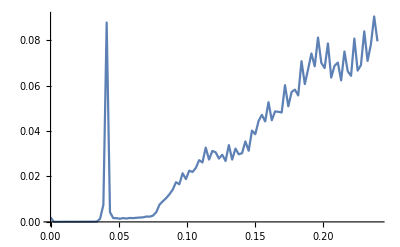

```mathematica
ListLinePlot[Re[NoiseList]]
```

```mathematica
NoiseList//MatrixForm
```

(0. | 0.0020025-0.246044 ⅈ
0.00242424 | 0.0000241085-0.0000114749 ⅈ
0.00484848 | 0.0000247254-2.85538×10^-6 ⅈ
0.00727273 | 0.0000454591-1.26984×10^-6 ⅈ
0.00969697 | 0.0000586472-7.11214×10^-7 ⅈ
0.0121212 | 0.0000593581-4.52252×10^-7 ⅈ
0.0145455 | 0.0000622214-3.11513×10^-7 ⅈ
0.0169697 | 0.0000679247-2.26542×10^-7 ⅈ
0.0193939 | 0.0000636819-1.71224×10^-7 ⅈ
0.0218182 | 0.000078215-1.33051×10^-7 ⅈ
0.0242424 | 0.0000670919-1.05399×10^-7 ⅈ
0.0266667 | 0.0000897411-8.44446×10^-8 ⅈ
0.0290909 | 0.000076863-6.77676×10^-8 ⅈ
0.0315152 | 0.000105036-5.36005×10^-8 ⅈ
0.0339394 | 0.000111174-4.0211×10^-8 ⅈ
0.0363636 | 0.00138629-1.87541×10^-7 ⅈ
0.0387879 | 0.00752284-8.75623×10^-7 ⅈ
0.0412121 | 0.0878181-3.40364×10^-6 ⅈ
0.0436364 | 0.00424154-2.60477×10^-7 ⅈ
0.0460606 | 0.00167864-1.14476×10^-7 ⅈ
0.0484848 | 0.00163413-7.52901×10^-8 ⅈ
0.0509091 | 0.00139463-5.78293×10^-8 ⅈ
0.0533333 | 0.00167673-4.77629×10^-8 ⅈ
0.0557576 | 0.00148386-4.102×10^-8 ⅈ
0.0581818 | 0.00173357-3.60676×10^-8 ⅈ
0.0606061 | 0.00165159-3.22119×10^-8 ⅈ
0.0630303 | 0.00180433-2.90938×10^-8 ⅈ
0.0654545 | 0.00191867-2.65076×10^-8 ⅈ
0.0678788 | 0.00199217-2.43266×10^-8 ⅈ
0.070303 | 0.00235854-2.24697×10^-8 ⅈ
0.0727273 | 0.00230756-2.12595×10^-8 ⅈ
0.0751515 | 0.0027438-2.01538×10^-8 ⅈ
0.0775758 | 0.00424417-1.34155×10^-7 ⅈ
0.08 | 0.00760663-3.04594×10^-7 ⅈ
0.0824242 | 0.0090735-4.03029×10^-7 ⅈ
0.0848485 | 0.0104491-4.23093×10^-7 ⅈ
0.0872727 | 0.0121601-4.40414×10^-7 ⅈ
0.089697 | 0.0142153-4.47197×10^-7 ⅈ
0.0921212 | 0.0174821-4.46023×10^-7 ⅈ
0.0945455 | 0.0165694-4.38849×10^-7 ⅈ
0.0969697 | 0.0214178-4.27002×10^-7 ⅈ
0.0993939 | 0.0188401-4.11352×10^-7 ⅈ
0.101818 | 0.0225676-3.92421×10^-7 ⅈ
0.104242 | 0.0220029-3.70416×10^-7 ⅈ
0.106667 | 0.0237643-3.45179×10^-7 ⅈ
0.109091 | 0.0271892-3.15965×10^-7 ⅈ
0.111515 | 0.026181-2.80954×10^-7 ⅈ
0.113939 | 0.0327223-5.2542×10^-6 ⅈ
0.116364 | 0.0274451-0.0000104744 ⅈ
0.118788 | 0.0312485-0.0000136316 ⅈ
0.121212 | 0.0306623-0.0000159742 ⅈ
0.123636 | 0.0278931-0.0000179857 ⅈ
0.126061 | 0.0295633-0.000019644 ⅈ
0.128485 | 0.0268285-0.0000210831 ⅈ
0.130909 | 0.0338337-0.0000223518 ⅈ
0.133333 | 0.0274301-0.0000234834 ⅈ
0.135758 | 0.0322792-0.0000245015 ⅈ
0.138182 | 0.0297723-0.0000254239 ⅈ
0.140606 | 0.0302842-0.0000262643 ⅈ
0.14303 | 0.0354513-0.0000270335 ⅈ
0.145455 | 0.0313244-0.0000277399 ⅈ
0.147879 | 0.040202-0.0000283898 ⅈ
0.150303 | 0.0386272-0.0000289884 ⅈ
0.152727 | 0.0444582-0.0000295507 ⅈ
0.155152 | 0.0471434-0.0000300731 ⅈ
0.157576 | 0.0442545-0.0000305595 ⅈ
0.16 | 0.0527284-0.000031013 ⅈ
0.162424 | 0.0447647-0.0000314365 ⅈ
0.164848 | 0.0486624-0.0000318325 ⅈ
0.167273 | 0.0484734-0.000032203 ⅈ
0.169697 | 0.0481948-0.00003255 ⅈ
0.172121 | 0.0602088-0.0000328752 ⅈ
0.174545 | 0.0509029-0.0000331801 ⅈ
0.17697 | 0.0572352-0.0000334659 ⅈ
0.179394 | 0.0582463-0.000033734 ⅈ
0.181818 | 0.0556889-0.0000339854 ⅈ
0.184242 | 0.0707688-0.0000342211 ⅈ
0.186667 | 0.0607012-0.0000344418 ⅈ
0.189091 | 0.0672669-0.0000346484 ⅈ
0.191515 | 0.0741924-0.0000348416 ⅈ
0.193939 | 0.0685307-0.000035022 ⅈ
0.196364 | 0.0812073-0.0000351902 ⅈ
0.198788 | 0.0700362-0.0000353466 ⅈ
0.201212 | 0.0677492-0.0000354917 ⅈ
0.203636 | 0.07862-0.0000356259 ⅈ
0.206061 | 0.0635644-0.0000357496 ⅈ
0.208485 | 0.0687494-0.0000358629 ⅈ
0.210909 | 0.0701586-0.0000359661 ⅈ
0.213333 | 0.0623308-0.0000360595 ⅈ
0.215758 | 0.0750385-0.000036143 ⅈ
0.218182 | 0.0663301-0.0000362169 ⅈ
0.220606 | 0.0643343-0.0000362812 ⅈ
0.22303 | 0.0807525-0.0000363357 ⅈ
0.225455 | 0.0666383-0.0000363805 ⅈ
0.227879 | 0.0690432-0.0000364154 ⅈ
0.230303 | 0.0839195-0.0000364402 ⅈ
0.232727 | 0.0708959-0.0000364544 ⅈ
0.235152 | 0.0780973-0.0000364565 ⅈ
0.237576 | 0.09048-0.0000364474 ⅈ
0.24 | 0.0795349-0.0000364261 ⅈ)